# Pruebas de caminatas cuánticas con una moneda de 4 dimensiones.

## DiscreteProbabilityPlot: estados, probabilidades y escalas de color

Evalúa las celdas en orden. Se carga QWMisc.wl desde la carpeta de este notebook y JA_libs desde el proyecto. VisualizeWalkerState permanece como interfaz de compatibilidad. Las probabilidades se representan sin renormalizarlas. La paleta predeterminada va de blanco (mínimo) a negro (máximo); ColorFunction permite elegir otra paleta.

## Llamar paquetes y ciertas funciones

```mathematica
root = NotebookDirectory[];
If[FindFile["ForScience`"] === $Failed,
  dependencyDirectosry = CreateDirectory[];
  ExtractArchive[FileNameJoin[{root, "JA_libs", "ForScience-0.88.45.paclet"}], dependencyDirectory];
  PacletDirectoryLoad[FileNameJoin[{dependencyDirectory, "ForScience-0.88.45"}]];
];
Needs["ForScience`"];
PacletDirectoryLoad[{
  FileNameJoin[{root, "JA_libs", "QuantumWalks"}],
  FileNameJoin[{root, "JA_libs", "QMB"}]
}];
Needs["QuantumWalks`"];
Needs["QuantumWalks`Billiards`"];
Needs["QMB`"];
Get[FileNameJoin[{root, "QWMisc.wl"}]];
```

Set::write: Tag PlotGrid in Options[PlotGrid] is Protected.

SetDelayed::write: Tag PlotGrid in PlotGrid[l_?(MatrixQ[#1,ValidGraphicsQ[«1»]||SameQ[«2»]&]&),o:OptionsPattern[{Alignment→Automatic,AspectRatio→Full,Axes→Automatic,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaseStyle→{},Frame→Automatic,FrameStyle→{},FrameTicks→Automatic,GridLines→None,GridLinesStyle→{},«27»,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,«16»}]] is Protected.

$Aborted

Get::noopen: Cannot open QuantumWalks`Billiards`.

Needs::nocont: Context QuantumWalks`Billiards` was not created when Needs was evaluated.

Remove::rmnsm: There are no symbols matching "ForScience`PlotUtils`PlotGrid".

General::stop: Further output of Remove::rmnsm will be suppressed during this calculation.

Set::write: Tag PlotGrid in Options[PlotGrid] is Protected.

SetDelayed::write: Tag PlotGrid in PlotGrid[l_?(MatrixQ[#1,ValidGraphicsQ[«1»]||SameQ[«2»]&]&),o:OptionsPattern[{Alignment→Automatic,AspectRatio→Full,Axes→Automatic,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaseStyle→{},Frame→Automatic,FrameStyle→{},FrameTicks→Automatic,GridLines→None,GridLinesStyle→{},«27»,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,«16»}]] is Protected.

```mathematica
Get["/Users/saul/Desktop/QWProgramming/plot_entropia_monedas.wl"]
```

```mathematica
RandomMatrix[name_String]:=Module[{u,o,oo,b,p},Switch[ToLowerCase[name],"o",RandomVariate[CircularOrthogonalMatrixDistribution[4]],"oo",KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]],"u",RandomVariate[CircularUnitaryMatrixDistribution[4]],"uoou",u=RandomVariate[CircularUnitaryMatrixDistribution[4]];
oo=KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]];
u.oo.ConjugateTranspose[u],"b",1/Sqrt[2] {{1,1,0,0},{0,0,1,1},{0,0,1,-1},{1,-1,0,0}},"ubu",u=RandomVariate[CircularUnitaryMatrixDistribution[4]];
b=1/Sqrt[2] {{1,1,0,0},{0,0,1,1},{0,0,1,-1},{1,-1,0,0}};
u.b.ConjugateTranspose[u],"p",DiagonalMatrix[Exp[I*RandomReal[{0,2 Pi},4]]],"gpg",p=DiagonalMatrix[Exp[I*RandomReal[{0,2 Pi},4]]];
GeneralizedGroverCoin[Pi/4.].p.ConjugateTranspose[GeneralizedGroverCoin[Pi/4.]],"upu",u=RandomVariate[CircularUnitaryMatrixDistribution[4]];
p=DiagonalMatrix[Exp[I*RandomReal[{0,2 Pi},4]]];
u.p.ConjugateTranspose[u],_,Message[RandomMatrix::name,name];
$Failed]];

RandomMatrix::name="Unknown matrix name `1`. Valid names are: o, oo, u, uoou, b, ubu, p, gpg, upu.";

ClearAll[RandomMatrixNames];

RandomMatrixNames[]:={"p","oo","b","gpg","o","uoou","ubu","u","upu"};
```

```mathematica
coinDiag=DiagonalMatrix[{0.1,0.2,0.3,0.4}];
v=RandomVariate[CircularOrthogonalMatrixDistribution[4]];
coinOp=v.coinDiag.ConjugateTranspose[v];
```

## Ejemplos de funciones, testeos y cosas similares.

## IPR espacial y densidad local I_n(x,y)

Se suma sobre la moneda antes de elevar al cuadrado. La densidad local I_n es una magnitud en posición, distinta de la distribución de Husimi en espacio de fases.

ComputeSpatialIPR[psi, d] devuelve un escalar; 
ComputeSpatialIPRDensity[psi, d] devuelve un valor por sitio, en el orden de grid["Coords"]. Ambas normalizan internamente y usan d = 4 por defecto. Los bloques consecutivos de d amplitudes corresponden a un sitio. La densidad se pasa a DiscreteProbabilityPlot como Probabilities, con escala Linear: Squared volvería a elevar I_n al cuadrado.

### 1. Estados localizado, uniforme y gaussiano

```mathematica
iprGrid=GenerateRectangleBasis[8,5];iprCoin=Normalize[{1,ⅈ,-1,0}];iprN=iprGrid["Dimension"];iprLocalized=LocalizedState[iprGrid,{2,3},iprCoin];iprUniform=Flatten[KroneckerProduct[ConstantArray[1/(√iprN),iprN],iprCoin]];iprGaussian=GaussianState[iprGrid,{2,3},iprCoin,1.2];iprStates={iprLocalized,iprUniform,iprGaussian};iprNames={"Localizado","Uniforme","Gaussiano"};iprProbabilities=(Total[Partition[Abs[Normal[#1]/Norm[#1]]^2,4],{2}]&)/@iprStates;iprDensities=ComputeSpatialIPRDensity/@iprStates;iprTotals=ComputeSpatialIPR/@iprStates;Grid[Prepend[MapThread[{#1,#2,Total[#3]}&,{iprNames,iprTotals,iprDensities}],{"Estado","IPR espacial","Suma de I_n"}],Frame->All]
```

Estado | IPR espacial | Suma de I_n
Localizado | 1 | 1
Uniforme | 1/54 | 1/54
Gaussiano | 0.111294 | 0.111294

El localizado tiene IPR = 1; el uniforme tiene IPR = 1/N y densidad 1/N^2 por sitio. El rectángulo incluye x = 0,...,8 e y = 0,...,5: N = 54. Cada mapa usa su propio rango de color para mostrar su estructura.

```mathematica
GraphicsGrid[Table[{DiscreteProbabilityPlot[iprGrid,iprProbabilities⟦j⟧,PlotLabel->iprNames⟦j⟧" : P_n(x,y)",ImageSize->420],DiscreteProbabilityPlot[iprGrid,iprDensities⟦j⟧,"InputType"->"Probabilities","ProbabilityScale"->"Linear",PlotLabel->iprNames⟦j⟧" : I_n(x,y) = P_n(x,y)^2; IPR = "N[iprTotals⟦j⟧],PlotLegends->Placed[BarLegend[{GrayLevel[1-#1]&,{0,Max[iprDensities⟦j⟧]}},LegendLabel->"I_n = P_n^2"],Right],ImageSize->420]},{j,Length[iprStates]}],ImageSize->1100]
```

-Graphics-

### 2. Ejemplo con un eigenvector del operador de evolución

```mathematica
iprEigenGrid=GenerateRectangleBasis[4,3];iprEigenCoin=N[FourierMatrix[4]];iprEvolution=BuildShiftOperators[iprEigenGrid,CoinDimension->4].KroneckerProduct[IdentityMatrix[iprEigenGrid["Dimension"],SparseArray],iprEigenCoin];{iprEigenvalues,iprEigenvectors}=Eigensystem[N[Normal[iprEvolution]]];iprEigenOrder=Ordering[Arg[iprEigenvalues]];iprEigenIndex=iprEigenOrder⟦Ceiling[Length[iprEigenOrder]/2]⟧;iprEigenstate=Normalize[iprEigenvectors⟦iprEigenIndex⟧];iprEigenP=Total[Partition[Abs[iprEigenstate]^2,4],{2}];iprEigenDensity=ComputeSpatialIPRDensity[iprEigenstate];iprEigenTotal=ComputeSpatialIPR[iprEigenstate];{"Eigenfase epsilon = -Arg(lambda)"->-Arg[iprEigenvalues⟦iprEigenIndex⟧],"IPR espacial"->iprEigenTotal,"Suma de I_n"->Total[iprEigenDensity],"Residuo del eigenvector"->Norm[iprEvolution.iprEigenstate-iprEigenvalues⟦iprEigenIndex⟧ iprEigenstate]}
```

```mathematica
GraphicsRow[{DiscreteProbabilityPlot[iprEigenGrid,iprEigenP,PlotLabel->"P_n(x,y) del eigenvector",ImageSize->420],DiscreteProbabilityPlot[iprEigenGrid,iprEigenDensity,"ProbabilityScale"->"Linear",PlotLabel->"Densidad local I_n(x,y)",PlotLegends->Placed[BarLegend[{GrayLevel[1-#1]&,{0,Max[iprEigenDensity]}},LegendLabel->"I_n = P_n^2"],Right],ImageSize->420]},ImageSize->1100]
```

### 3. Comprobaciones automáticas

```mathematica
iprTestReport=TestReport[{VerificationTest[ComputeSpatialIPR[iprLocalized],1,TestID->"IPR localizada"],VerificationTest[ComputeSpatialIPR[iprUniform],1/iprN,TestID->"IPR uniforme"],VerificationTest[ComputeSpatialIPRDensity[iprUniform],ConstantArray[1/iprN^2,iprN],TestID->"Densidad uniforme"],VerificationTest[Max[Abs[iprDensities⟦3⟧-iprProbabilities⟦3⟧^2]]<1/10^12,True,TestID->"I_n = P_n^2"],VerificationTest[Abs[Total[iprEigenDensity]-iprEigenTotal]<1/10^12,True,TestID->"Suma local = IPR del eigenvector"],VerificationTest[Norm[iprEvolution.iprEigenstate-iprEigenvalues⟦iprEigenIndex⟧ iprEigenstate]<1/10^10,True,TestID->"Eigenvector válido"],VerificationTest[And@@(1/iprN-1/10^12≤#1≤1+1/10^12&)/@iprTotals,True,TestID->"Cotas 1/N <= IPR <= 1"],VerificationTest[ComputeSpatialIPRDensity[SparseArray[{2->ⅈ,7->2},{8}]],{1/25,16/25},TestID->"Estado disperso complejo"],VerificationTest[ComputeSpatialIPRDensity[7 ⅈ {1,ⅈ,0,2},2],{1/9,4/9},TestID->"Invariancia bajo reescalamiento"],VerificationTest[ComputeSpatialIPRDensity[{1,ⅈ,0,2},1],{1/36,1/36,0,4/9},TestID->"Dimensión de moneda 1"],VerificationTest[{ComputeSpatialIPR[{1,ⅈ,0,0}/(√2)],Total[Abs[{1,ⅈ,0,0}/(√2)]^4]},{1,1/2},TestID->"IPR espacial distinta de posición-moneda"],VerificationTest[Quiet[ComputeSpatialIPR[ConstantArray[0,8]]],$Failed,TestID->"Rechazo del vector cero"],VerificationTest[Quiet[ComputeSpatialIPRDensity[{1,2,3}]],$Failed,TestID->"Rechazo de longitud incompatible"],VerificationTest[Quiet[ComputeSpatialIPR[{1,2},0]],$Failed,TestID->"Rechazo de dimensión de moneda inválida"],VerificationTest[Quiet[ComputeSpatialIPR[{∞,0},2]],$Failed,TestID->"Rechazo de amplitudes no finitas"]}];iprTestReport
```

## Evolución de la IPR espacial

SpatialIPREvolutionPlot[operador, estadoInicial, pasos] grafica la IPR desde t = 0 hasta el paso indicado. CoinDimension -> 4 es el valor predeterminado. Se conserva solo el estado actual durante la evolución. La escala vertical es logarítmica y la línea discontinua indica 1/N, el mínimo de la IPR para N nodos; no es una predicción del valor final.

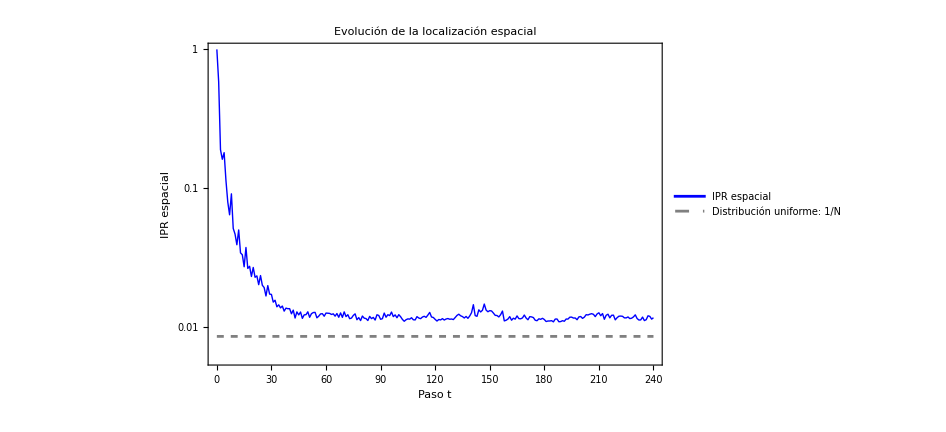

```mathematica
iprPlotGrid=GenerateRectangleBasis[12,8];iprPlotCoin=N[FourierMatrix[4]];iprPlotEvolution=BuildShiftOperators[iprPlotGrid,CoinDimension->4].KroneckerProduct[IdentityMatrix[iprPlotGrid["Dimension"],SparseArray],SparseArray[iprPlotCoin]];iprPlotInitial=LocalizedState[iprPlotGrid,{6,4},Normalize[{1,ⅈ,-1,0}]];SpatialIPREvolutionPlot[iprPlotEvolution,iprPlotInitial,240]
```

Para el operador evolutionSep y el estado initialState de tu rutina, basta llamar SpatialIPREvolutionPlot[evolutionSep, initialState, steps]. No necesitas finalstates ni iprDat. Las opciones de ListLinePlot permiten cambiar etiquetas, tamaño, estilos y rango.

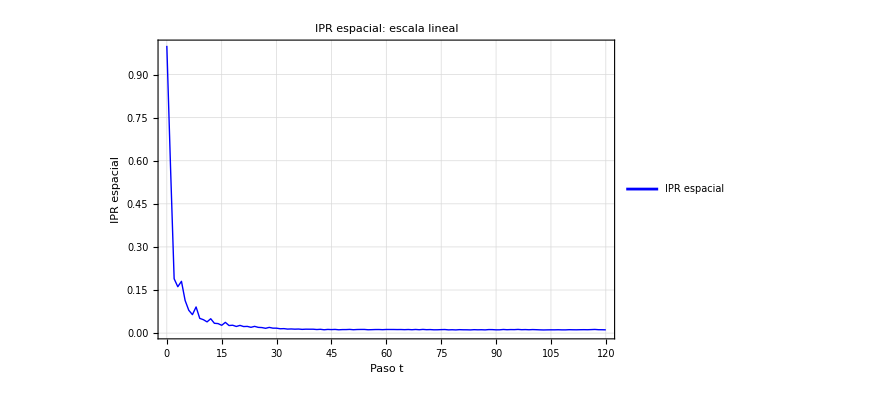

```mathematica
SpatialIPREvolutionPlot[iprPlotEvolution,iprPlotInitial,120,ScalingFunctions->None,"ShowUniformReference"->False,PlotLabel->"IPR espacial: escala lineal",ImageSize->650]
```

ComputeSpatialIPREvolution devuelve los pares {t, IPR(t)} si necesitas guardar o analizar los datos. Para cambiar la dimensión de moneda, usa CoinDimension -> 2 (o la dimensión correspondiente) en cualquiera de las dos funciones.

```mathematica
iprEvolutionData=ComputeSpatialIPREvolution[iprPlotEvolution,iprPlotInitial,120];{"Número de muestras"->Length[iprEvolutionData],"Primera muestra"->First[iprEvolutionData],"Última muestra"->Last[iprEvolutionData]}
```

{Número de muestras→121,Primera muestra→{0,1.},Última muestra→{120,0.0113371}}

### Comprobaciones de evolución

```mathematica
iprEvolutionTestReport=TestReport[{VerificationTest[ComputeSpatialIPREvolution[IdentityMatrix[8,SparseArray],{1,0,0,0,0,0,0,0},3],{{0,1.},{1,1.},{2,1.},{3,1.}},TestID->"Identidad y tiempos desde cero"],VerificationTest[ComputeSpatialIPREvolution[IdentityMatrix[8,SparseArray],ConstantArray[1,8],0],{{0,0.5}},TestID->"Cero pasos y estado no normalizado"],VerificationTest[Max[Abs[ComputeSpatialIPREvolution[N[FourierMatrix[4]],{1,0,0,0},5,CoinDimension->2]⟦All,2⟧-(ComputeSpatialIPR[#1,2]&)/@NestList[N[FourierMatrix[4]].#1&,{1.,0.,0.,0.},5]]]<1/10^12,True,TestID->"CoinDimension 2 y comparación con NestList"],VerificationTest[Quiet[ComputeSpatialIPREvolution[IdentityMatrix[8],ConstantArray[0,8],3]],$Failed,TestID->"Estado cero"],VerificationTest[Quiet[ComputeSpatialIPREvolution[IdentityMatrix[4],ConstantArray[1,8],3]],$Failed,TestID->"Dimensiones incompatibles"],VerificationTest[Quiet[ComputeSpatialIPREvolution[IdentityMatrix[8],ConstantArray[1,8],-1]],$Failed,TestID->"Pasos negativos"],VerificationTest[Quiet[ComputeSpatialIPREvolution[ConstantArray[0,{8,8}],ConstantArray[1,8],2]],$Failed,TestID->"Evolución a estado cero"]}];iprEvolutionTestReport
```

## 1. Estado o probabilidades: misma imagen

```mathematica
grid=GenerateRectangleBasis[8,5];
coin=Normalize[{1,ⅈ,-1,0}];
psi=GaussianState[grid,{2,3},coin,1.2];
probabilities=Total[Partition[Abs[Normal[psi]]^2,4],{2}];
statePlot=DiscreteProbabilityPlot[grid,psi,"InputType"->"State",PlotLegends->None];
probabilityPlot=DiscreteProbabilityPlot[grid,probabilities,PlotLegends->None];
{statePlot===probabilityPlot,Total[probabilities]}
```

{True,1.}

```mathematica
GraphicsRow[{DiscreteProbabilityPlot[grid,psi,"InputType"->"State",PlotLabel->"Desde amplitudes",ImageSize->360],DiscreteProbabilityPlot[grid,probabilities,PlotLabel->"Desde probabilidades",ColorFunction->"DarkRainbow",ImageSize->360]},ImageSize->900]
```

-Graphics-

## 2. Escalas de color

```mathematica
grid=GenerateRectangleBasis[8,5];
coin=Normalize[{1,ⅈ,-1,0}];
psi=GaussianState[grid,{2,3},coin,1.2];
```

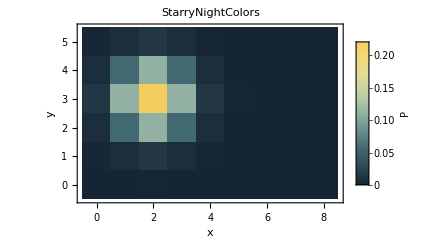
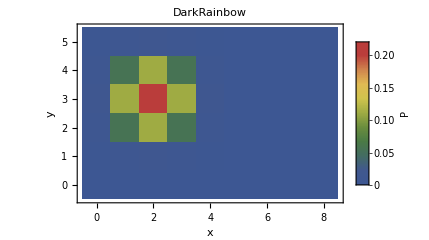
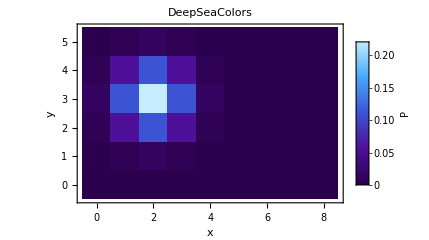
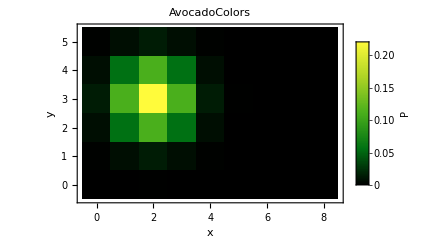
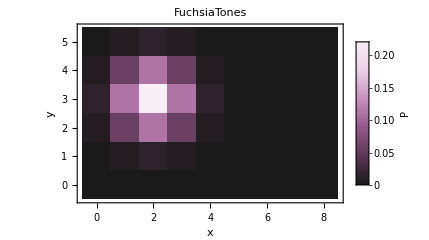
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
colores={"StarryNightColors","DarkRainbow","DeepSeaColors","AvocadoColors","FuchsiaTones"};
{DiscreteProbabilityPlot[grid,psi,"InputType"->"State",PlotLabel->"Default",ImageSize->360],Flatten[DiscreteProbabilityPlot[grid,psi,"InputType"->"State",PlotLabel->#,ColorFunction->#,ImageSize->360]&/@colores]}
```

## 3. Escala de probabilidad

Cada leyenda indica la cantidad transformada. ProbabilityRange siempre recibe probabilidades originales. Squared se conserva por compatibilidad; Sqrt y CubeRoot resaltan regiones de baja probabilidad.

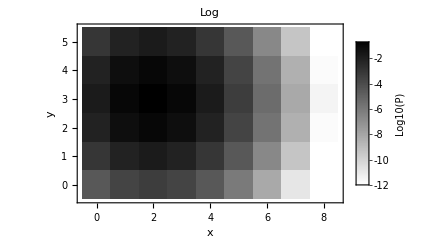
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
grid=GenerateRectangleBasis[8,5];
coin=Normalize[{1,ⅈ,-1,0}];
psi=GaussianState[grid,{2,3},coin,1.2];

scales={"Linear","Sqrt","CubeRoot","Squared","Log"};
{DiscreteProbabilityPlot[grid,psi,"InputType"->"State",PlotLabel->"Default",ImageSize->360],Flatten[DiscreteProbabilityPlot[grid,psi,"InputType"->"State",PlotLabel->#,"ProbabilityScale"->#,ImageSize->360]&/@scales]}
```

## 4. Evolución con escala automática por estado

Cada cuadro ajusta la escala de color a su propia probabilidad máxima. Esto permite distinguir las variaciones espaciales aunque las probabilidades sean pequeñas. Un mismo color puede corresponder a probabilidades distintas entre cuadros; consulta la leyenda de cada uno.

```mathematica
SeedRandom[23];
Lx=20; Ly=20;
grid=GenerateRectangleBasis[Lx,Ly];
pos={6,6};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];
steps=10;
stride=1;
coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionSep=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinSep//N]];
initialState=LocalizedState[grid,pos,coin];
QWAnimation[grid,evolutionSep,initialState,steps,"FrameStride"->stride,PlotLabel->"Separable",ImageSize->500,LabelStyle->Directive[Bold,17],AnimationRunning->True]
```

### VIendo moneda separable vs no separable

```mathematica
SeedRandom[13];
Lx=70; Ly=70;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];

coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionSep=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinSep//N]];

coinNoSep=N[RandomVariate[CircularOrthogonalMatrixDistribution[4]]];
evolutionNoSep=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinNoSep//N]];

initialState=LocalizedState[grid,pos,coin];

steps=500;
stride=1;

Grid[{{QWAnimation[grid,evolutionSep,initialState,steps,"FrameStride"->stride,PlotLabel->"OO",ImageSize->500,LabelStyle->Directive[Bold,17],AnimationRunning->True],QWAnimation[grid,evolutionNoSep,initialState,steps,"FrameStride"->stride,PlotLabel->"O",ImageSize->500,LabelStyle->Directive[Bold,17],AnimationRunning->True]}},Alignment->{Center,Top},Spacings->{2,0}]
```

$Aborted

## 5. Distribución temporal promedio

```mathematica
SeedRandom[13];
Lx=70; Ly=70;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];

coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionOp=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinSep//N]];

Tmax=9000;
initialState=LocalizedState[grid,pos,coin];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution]
```

### Comparando diferentes monedas

```mathematica
RandomMatrixNames[]
```

{p,oo,b,gpg,o,uoou,ubu,u,upu}

```mathematica
Lx=70; Ly=70;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];
Tmax=9000;
Module[{c=RandomMatrix[#],evolutionOp,distribution},
evolutionOp=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[c//N]];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution,PlotLabel->#,LabelStyle->Directive[Bold, 17],ImageSize->450]
]&/@RandomMatrixNames[]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## 6. Autovalores de tres rectangulos de distinto tamaño

### Preparar QuantumWalks en cada kernel

La ruta corresponde a la copia de QuantumWalks que ya existe en tu cuenta del cluster. PacletDirectoryLoad solo la hace visible durante la sesion temporal. Se carga ForScience y luego QuantumWalks en cada kernel del nodo. El bloque de FormatUsage evita un problema de formato de ayudas cuando no hay interfaz grafica en el nodo.

```mathematica
prepararQuantumWalks = Function[
  Module[{ruta = "/home/saul/QW/JA_libs/QuantumWalks"},
    If[DirectoryQ[ruta],
      PacletDirectoryLoad[ruta];
      Needs["ForScience`"];
      Block[{ForScience`PacletUtils`FormatUsage = Identity}, Needs["QuantumWalks`"]];
      MemberQ[$Packages, "ForScience`"] &&
        Length[DownValues[QuantumWalks`Billiards`GenerateRectangleBasis]] > 0,
      False
    ]
  ]
];
```

### Definir una diagonalizacion por cada rectangulo

Cada entrada {ancho, alto} cuenta posiciones, no indices maximos. GenerateRectangleBasis[ancho-1, alto-1] produce ancho x alto posiciones. Con cuatro estados de moneda, el operador U = S . (I KroneckerProduct C) tiene dimension 4 ancho alto. Se calculan todos los autovalores de la matriz densa; esta eleccion solo es razonable mientras quepa en la memoria del nodo.

```mathematica
calcularEspectro = Function[par,
  Module[{base, dim, s, moneda, u, vals},
    base = QuantumWalks`Billiards`GenerateRectangleBasis[par[[1]] - 1, par[[2]] - 1];
    dim = base["Dimension"];
    s = QuantumWalks`Billiards`BuildShiftOperators[base,
      QuantumWalks`Billiards`CoinDimension -> 4];
    moneda = QuantumWalks`Billiards`GeneralizedGroverCoin[Pi/4.];
    u = s . KroneckerProduct[IdentityMatrix[dim, SparseArray], SparseArray[moneda]];
    vals = Eigenvalues[Normal[u]];
    <|"Nodo" -> $MachineName, "Proceso" -> $ProcessID,
      "Tamano" -> par, "DimensionU" -> Dimensions[u],
      "Autovalores" -> vals, "ErrorModulo" -> Max[Abs[Abs[vals] - 1]]|>
  ]
];
```

### Ejecutar cuatro trabajos en dos kernels

```mathematica
resultados = EjecutarEnNodo["nodo1", 2, calcularEspectro,
  {{3, 2}, {4, 2}, {5, 2}, {6, 2}}, prepararQuantumWalks];
```

From (kernel 2):

GenerateRectangleBasis::shdw: 
   Symbol GenerateRectangleBasis appears in multiple contexts 
    {QuantumWalks`Billiards`, Global`}; definitions in context 
    QuantumWalks`Billiards` may shadow or be shadowed by other definitions.

From (kernel 1):

GenerateRectangleBasis::shdw: 
   Symbol GenerateRectangleBasis appears in multiple contexts 
    {QuantumWalks`Billiards`, Global`}; definitions in context 
    QuantumWalks`Billiards` may shadow or be shadowed by other definitions.

Cada entrada se calcula completa en un kernel. Los resultados regresan en el mismo orden de la lista de entradas. Los identificadores de proceso permiten comprobar que participaron dos kernels. ErrorModulo mide cuanto se aleja el modulo de cada autovalor de 1.

```mathematica
If[ListQ[resultados],
  resultados[[All, {"Tamano", "Nodo", "Proceso", "DimensionU", "ErrorModulo"}]],
  resultados
]
```

Failure[…]

```mathematica
If[ListQ[resultados],
  {DeleteDuplicates[resultados[[All, "Proceso"]]],
   Length /@ resultados[[All, "Autovalores"]]},
  resultados
]
```

{{2803001,2803175},{1,1,1,1}}

# Aplicaciones:

## IPR

## Rectangulo

### Visualizando un caso particular. Graficando la densidad de ipr y checando un valor particular de la densidad según un nodo dado.

```mathematica
Lx=20;Ly=20;
grid=GenerateRectangleBasis[Lx,Ly];
pos={10,10};
coin=HaarRandomState[4];
initState=Normalize[LocalizedState[grid,pos,coin]+LocalizedState[grid,pos+{1,1},coin]];

iprdensity=ComputeSpatialIPRDensity[initState,4];

indexList=grid["Mapping"];
index=indexList[{10,10}];
iprlocal=iprdensity[[index]]
DiscreteProbabilityPlot[grid,iprdensity]
```

0.25

-Graphics-

### Comparando IPRs

#### Para estados localizados

Para dimensiones comparables con el sinai

```mathematica
L1=140;R1=100;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

Las dimensiones del rectangulo serían:Lx= 97, Ly= 60

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=97;
Ly=60;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=2000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
iprDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];
ComputeSpatialIPREvolution[evolutionOp,initialState,Tmax,CoinDimension->4]]&/@names;
```

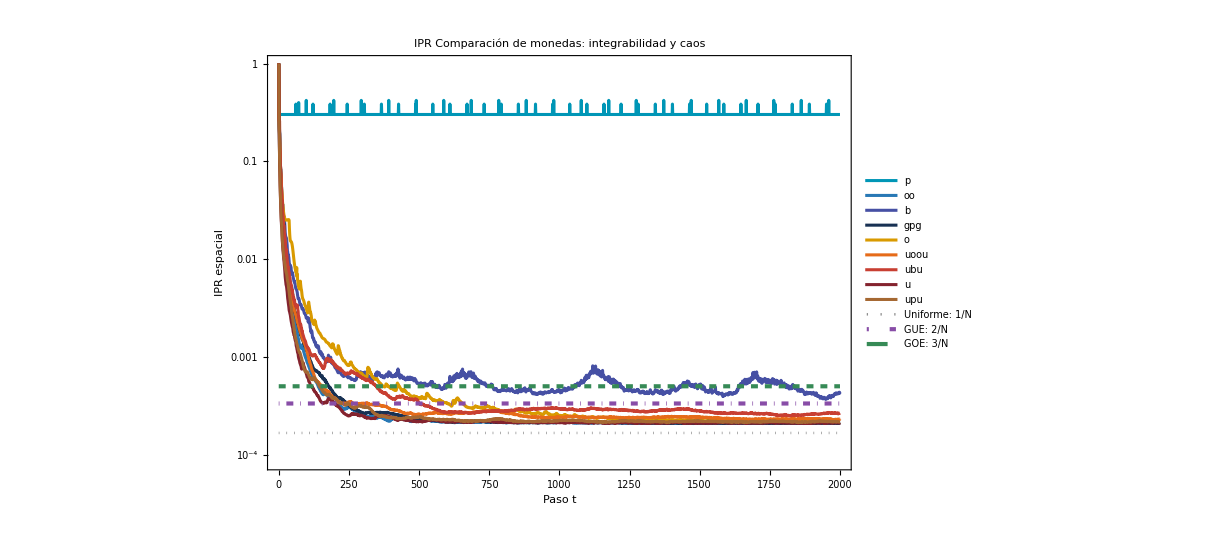

```mathematica
(*Clasificación:integrables hasta "gpg" inclusive*)cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]   (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]   (*upu:cobre*)};
(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias horizontales:1/N,2/N y 3/N*)
referenceValues={1/nSites,2/nSites,3/nSites};

references=Table[{{0,value},{Tmax,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo.Se supone que cada curva de iprDat contiene puntos {t,IPR}.*)
tInset=0.75 Tmax;

lateData=Select[#,First[#]>=tInset&]&/@iprDat;

lateReferences=Table[{{tInset,value},{Tmax,value}},{value,referenceValues}];

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{All,{0.00015,0.001}},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->35];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],{"Uniforme: 1/N","GUE: 2/N","GOE: 3/N"},LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprDat,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR espacial"},PlotLabel->"IPR\nComparación de monedas: integrabilidad y caos",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.80,0.60}],Center,Scaled[{0.45,0.45}]]}],Placed[legend,Right]]
```

```mathematica
Export["/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/IPR_CompCoins_Localized_Rect.pdf",Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/IPR_CompCoins_Localized_Rect.pdf

#### Para estados deslocalizados

Para dimensiones comparables con el sinai

```mathematica
L1=120;R1=90;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

Las dimensiones del rectangulo serían:Lx= 80, Ly= 50

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=97;
Ly=60;
grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=RandomDelocalizedState[dim,4,"RandomSeed"->7];

Tmax=2000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
iprDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];
ComputeSpatialIPREvolution[evolutionOp,initialState,Tmax,CoinDimension->4]]&/@names;
```

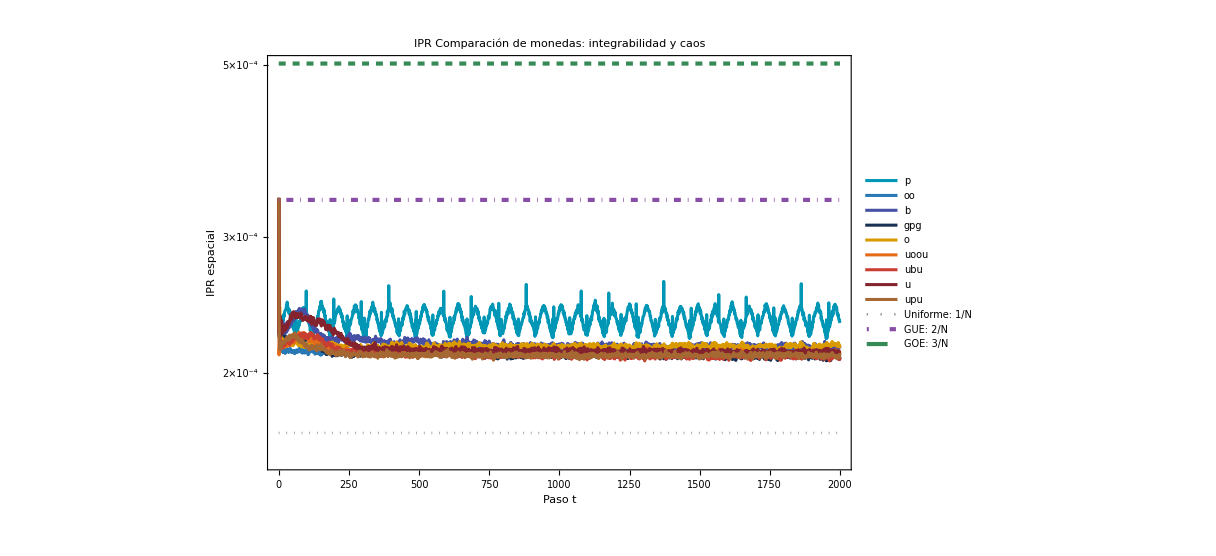

```mathematica
(*Clasificación:integrables hasta "gpg" inclusive*)cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]   (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]   (*upu:cobre*)};
(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias horizontales:1/N,2/N y 3/N*)
referenceValues={1/nSites,2/nSites,3/nSites};

references=Table[{{0,value},{Tmax,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo.Se supone que cada curva de iprDat contiene puntos {t,IPR}.*)
tInset=0.75 Tmax;

lateData=Select[#,First[#]>=tInset&]&/@iprDat;

lateReferences=Table[{{tInset,value},{Tmax,value}},{value,referenceValues}];

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{All,{0.00015,0.0006}},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->35];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],{"Uniforme: 1/N","GUE: 2/N","GOE: 3/N"},LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprDat,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR espacial"},PlotLabel->"IPR\nComparación de monedas: integrabilidad y caos",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.6,0.75}],Center,Scaled[{0.35,0.35}]]}],Placed[legend,Right]]
```

```mathematica
Export["/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/IPR_CompCoins_DeLocalized_Rect.pdf",Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/IPR_CompCoins_DeLocalized_Rect.pdf

### Densidad de IPR (Matrices Grandes)

#### Para eigenestados alrededor de un valor dado

Veamos la DoS y ver si cambio mucho con el tamaño

Eigenvalues::arh: Because finding 3844 out of the 3844 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

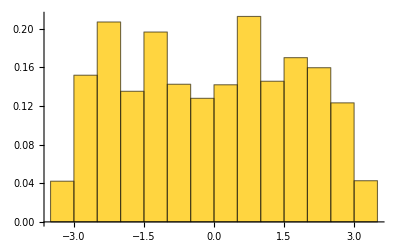

```mathematica
Lx=30;
Ly=30;
grid=GenerateRectangleBasis[Lx,Ly];

(*grid debe ser la malla del estadio*)
coinMatrix=N[RandomMatrix["upu"]];

S=BuildShiftOperators[grid,CoinDimension->4];

U=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinMatrix]];
eigenvals=U//Eigenvalues;
eigenphases=Arg[eigenvals];

Histogram[eigenphases,Automatic,"PDF"]
```

```mathematica
Lx=80;
Ly=60;
grid=GenerateRectangleBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["b"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinMatrix]]];

(*Parámetros ajustables*)
k=10;
columns=3;
epsilon0=0.4;

sigma=1.001 Exp[-I epsilon0];

(*Ajustar la base de Arnoldi al número solicitado*)
basisSize=Min[Length[U],Max[60,2 k+10]];

{eigenvalues,eigenvectors}=Eigensystem[U,-k,Method->{"Arnoldi","Shift"->sigma,"BasisSize"->basisSize,"MaxIterations"->5000,"Tolerance"->10^-10}];

eigenvectors=Normalize/@eigenvectors;
eigenphases=-Arg[eigenvalues];

(*Ordenar por eigenfase*)
order=Ordering[eigenphases];
eigenvalues=eigenvalues[[order]];
eigenvectors=eigenvectors[[order]];
eigenphases=eigenphases[[order]];

residuals=MapThread[Norm[U.#2-#1 #2]&,{eigenvalues,eigenvectors}];

nFound=Length[eigenvectors];

densities=ComputeSpatialIPRDensity[#,4]&/@eigenvectors;
iprValues=Total/@densities;

(*Resumen*)
summary=Grid[Prepend[Table[{j,NumberForm[eigenphases[[j]],{6,4}],ScientificForm[residuals[[j]],3],ScientificForm[iprValues[[j]],3]},{j,nFound}],{"Estado","ε","Residuo","IPR"}],Frame->All];

(*Un panel por eigenestado*)
plots=Table[DiscreteProbabilityPlot[grid,densities[[j]],"ProbabilityScale"->"Linear",PlotLabel->Column[{Row[{"Estado ",j,"; ε = ",NumberForm[eigenphases[[j]],{6,4}]}],Row[{"IPR = ",ScientificForm[iprValues[[j]],3]}]},Alignment->Center],ImageSize->350],{j,nFound}];

(*Completar únicamente los espacios vacíos de la última fila*)
rows=Ceiling[nFound/columns];

Column[{summary,GraphicsGrid[Partition[PadRight[plots,rows columns,Null],columns],Spacings->{0.4,0.6},ImageSize->400 columns]}]

GraphicsGrid[Partition[PadRight[plots,6,Null],3],Spacings->{0.4,0.6},ImageSize->1200]
```

Estado | ε | Residuo | IPR
1 | 0.3979 | 3.74×10^-14 | 2.92×10^-4
2 | 0.3980 | 3.92×10^-14 | 2.61×10^-4
3 | 0.3983 | 4.15×10^-14 | 2.61×10^-4
4 | 0.3987 | 4.58×10^-14 | 2.97×10^-4
5 | 0.3997 | 3.74×10^-14 | 2.72×10^-4
6 | 0.4002 | 3.29×10^-14 | 3.22×10^-4
7 | 0.4013 | 3.56×10^-14 | 2.99×10^-4
8 | 0.4016 | 3.64×10^-14 | 3.1×10^-4
9 | 0.4018 | 4.21×10^-14 | 2.6×10^-4
10 | 0.4021 | 3.65×10^-14 | 3.11×10^-4
-Graphics-

-Graphics-

#### Tomando eigenestados en puntos distintos del espectro de energías

```mathematica
(*Malla y operador de evolución*)Lx=80;
Ly=80;
grid=GenerateRectangleBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["upu"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinMatrix]]];

(*Seis intervalos y sus centros*)
k=10;
edges=Subdivide[-Pi,Pi,k];
intervals=Partition[edges,2,1];
targets=Mean/@intervals;

(*Un eigenestado próximo al centro de cada intervalo*)
eigenData=Table[Module[{sigma,vals,vecs,psi,phase,residual},sigma=1.001 Exp[-I targets[[j]]];
{vals,vecs}=Check[Eigensystem[U,-1,Method->{"Arnoldi","Shift"->sigma,"BasisSize"->60,"MaxIterations"->5000,"Tolerance"->10^-10}],Print["No convergió la búsqueda del intervalo ",j];
Abort[]];
psi=Normalize[First[vecs]];
phase=-Arg[First[vals]];
residual=Norm[U.psi-First[vals] psi];
(*No asignar a un intervalo un estado que quedó fuera*)If[!TrueQ[intervals[[j,1]]<=phase<=intervals[[j,2]]],Print["El eigenestado encontrado para el intervalo ",j," quedó fuera: ε = ",phase,". Revisa la búsqueda o si hay espectro en ese intervalo."];
Abort[]];
If[residual>10^-8,Print["Residuo demasiado grande en el intervalo ",j,": ",residual];
Abort[]];
{First[vals],psi,phase,residual}],{j,k}];

eigenvalues=eigenData[[All,1]];
eigenvectors=eigenData[[All,2]];
eigenphases=eigenData[[All,3]];
residuals=eigenData[[All,4]];

densities=ComputeSpatialIPRDensity[#,4]&/@eigenvectors;
iprValues=Total/@densities;

(*Resumen:objetivo,eigenfase encontrada,residuo e IPR*)
summary=Grid[Prepend[Table[{j,NumberForm[N[targets[[j]]],{6,4}],NumberForm[eigenphases[[j]],{6,4}],ScientificForm[residuals[[j]],3],ScientificForm[iprValues[[j]],3]},{j,k}],{"Intervalo","ε objetivo","ε encontrada","Residuo","IPR"}],Frame->All];
```

```mathematica
(*Configuración de la visualización*)columns=3;
nPlots=Length[eigenvectors];

(*Mapas con títulos externos y leyendas normalizadas*)
plots=Table[Module[{density,dmax,header,graphic},density=densities[[j]];
dmax=Max[density];
header=Row[{"Intervalo ",j,": ",NumberForm[N[intervals[[j,1]]],{4,2}]," a ",NumberForm[N[intervals[[j,2]]],{4,2}]}];
graphic=DiscreteProbabilityPlot[grid,density,"ProbabilityScale"->"Linear","ProbabilityRange"->{0,dmax},ColorFunction->(GrayLevel[1-#]&),PlotLabel->None,FrameLabel->{"x","y"},LabelStyle->Directive[Black,11],ImagePadding->{{45,15},{45,15}},ImageSize->320,PlotLegends->With[{upper=dmax},Placed[BarLegend[{Function[value,GrayLevel[1-Clip[value/upper,{0,1}]]],{0,upper}},LegendLabel->"Iₙ",LegendMarkerSize->{18,180},LabelStyle->Directive[Black,10]],Right]]];
Column[{Style[header,12,Bold],Style[Row[{"ε = ",NumberForm[eigenphases[[j]],{6,4}],"   IPR = ",ScientificForm[iprValues[[j]],3]}],11],Style[Row[{"Residuo = ",ScientificForm[residuals[[j]],2]}],10,GrayLevel[0.35]],graphic},Alignment->Center,Spacings->0.4]],{j,nPlots}];

(*Completar la última fila sin perder paneles*)
panel=Grid[Partition[PadRight[plots,columns Ceiling[nPlots/columns],""],columns],Alignment->{Center,Top},Spacings->{2,2}];

(*Una única imagen con todos los mapas*)
imagen=Rasterize[panel,"Image",ImageResolution->200];

imagen
```

-Graphics-

### Densidad de IPR (Matrices Pequeñas)

```mathematica
(*Malla y operador*)
Lx=30;
Ly=30;
grid=GenerateRectangleBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["b"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinMatrix]]];

(*Espectro completo:eigenvalores y vectores correspondientes*)
{eigenvalues,eigenvectors}=Eigensystem[Normal[U]];
eigenvectors=Normalize/@eigenvectors;
eigenphases=-Arg[eigenvalues];
```

```mathematica
(*Dividir las eigenfases en subintervalos*)nIntervals=15;
columns=3;

edges=N[Subdivide[-Pi,Pi,nIntervals]];
intervals=Partition[edges,2,1];
centers=Mean/@intervals;

(*Seleccionar un eigenestado cercano al centro de cada intervalo*)
selectedIndices=Table[Module[{candidates},candidates=Select[Range[Length[eigenphases]],Function[index,intervals[[j,1]]<=eigenphases[[index]]&&If[j==nIntervals,eigenphases[[index]]<=intervals[[j,2]],eigenphases[[index]]<intervals[[j,2]]]]];
If[candidates==={},Missing["EmptyInterval"],First[MinimalBy[candidates,Abs[eigenphases[[#]]-centers[[j]]]&]]]],{j,nIntervals}];

(*Construir cada panel*)
plots=Table[Module[{index,density,residual,header,graphic,dmax},index=selectedIndices[[j]];
header=Row[{"Intervalo ",j,": ",NumberForm[intervals[[j,1]],{4,2}]," a ",NumberForm[intervals[[j,2]],{4,2}]}];
If[MissingQ[index],Column[{Style[header,12,Bold],"Sin eigenestados"},Alignment->Center],density=ComputeSpatialIPRDensity[eigenvectors[[index]],4];
dmax=Max[density];
residual=Norm[U.eigenvectors[[index]]-eigenvalues[[index]] eigenvectors[[index]]];
graphic=DiscreteProbabilityPlot[grid,density,"ProbabilityScale"->"Linear","ProbabilityRange"->{0,dmax},ColorFunction->(GrayLevel[1-#]&),PlotLabel->None,FrameLabel->{"x","y"},LabelStyle->Directive[Black,11],ImagePadding->{{45,15},{45,15}},ImageSize->320,(*Leyenda:normalizar la densidad para asignar el color*)PlotLegends->With[{upper=dmax},Placed[BarLegend[{Function[value,GrayLevel[1-Clip[value/upper,{0,1}]]],{0,upper}},LegendLabel->"Iₙ",LegendMarkerSize->{18,180},LabelStyle->Directive[Black,10]],Right]]];
Column[{Style[header,12,Bold],Style[Row[{"ε = ",NumberForm[eigenphases[[index]],{6,4}],"   IPR = ",ScientificForm[Total[density],3]}],11],Style[Row[{"Residuo = ",ScientificForm[residual,2]}],10,GrayLevel[0.35]],graphic},Alignment->Center,Spacings->0.4]]],{j,nIntervals}];

(*Organizar los paneles*)
panel=Grid[Partition[PadRight[plots,columns Ceiling[nIntervals/columns],""],columns],Alignment->{Center,Top},Spacings->{2,2}];

(*Convertir el conjunto en una única imagen*)
imagen=Rasterize[panel,"Image",ImageResolution->200];

imagen
```

-Graphics-

### Tratando de hallar estados de borde mediante a IPR

```mathematica
SeedRandom[23];
Lx=30;
Ly=25;
grid=GenerateRectangleBasis[Lx,Ly];
S=BuildShiftOperators[grid,CoinDimension->4];
nSites=grid["Dimension"];
c=N[RandomMatrix["oo"]];
evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];

(*Eigenvalores y eigenvectores,en el mismo orden*)
{eigenvals,eigenvecs}=Eigensystem[Normal[evolutionOp]];
```

#### Chequeando IPR vs cuasiEnergía

{-2.47387,-2.47386,-2.42073,-2.42073,-2.34919,-2.34917,-2.31595,-2.31595,-2.27683,-2.27683,-2.14816,-0.229399,-0.229397,-0.190275,-0.190275,-0.157049,-0.157048,-0.0854979,-0.0854975,-0.0323694,-0.0323662,-0.00678915,-0.00677986,0.667703,0.667814,0.720865,0.72087,0.79236,0.79246,0.825642,0.825642,0.864774,0.8648,2.78338,2.91219,2.91219,2.95132,2.95132,2.98454,2.98455,3.0561,3.0561,3.10924,3.10924}

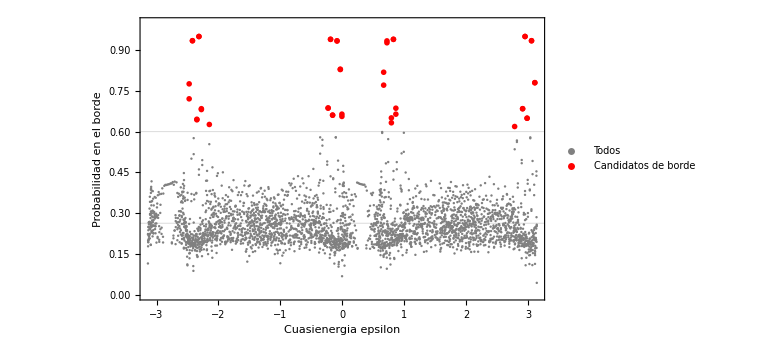

```mathematica
eigenenergies=Arg[eigenvals];
borde=AnalyzeBoundaryEigenstates[grid,eigenvals,eigenvecs,"BoundaryWidth"->2,"BoundaryThreshold"->0.6];
Dataset[borde["Candidates"]]
borde["CandidateEnergies"]
PlotBoundarySpectrum[borde]
```

```mathematica
candidatos=borde["CandidateEnergies"];
Module[{result},result=EigenstateAtEnergy[candidatos[[#]],eigenvals,eigenvecs];
DiscreteProbabilityPlot[grid,result["State"],"InputType"->"State",PlotLabel->"Desde amplitudes",ImageSize->200]]&/@Range[1,candidatos//Length]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Chequeando Histograma

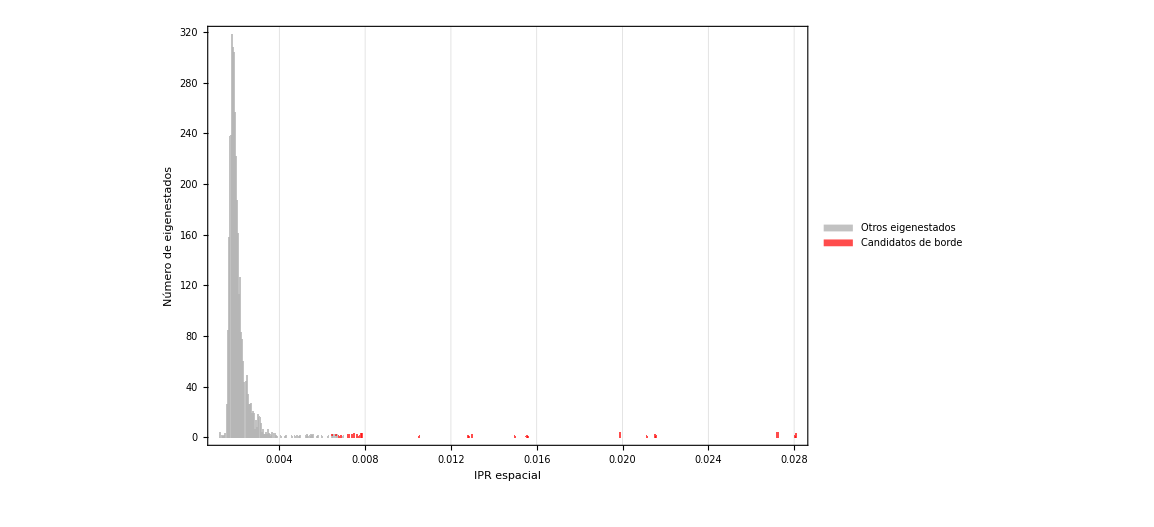

```mathematica
IPRdat=ComputeSpatialIPR[#,4]&/@eigenvecs;

indicesBorde=borde["CandidateIndices"];
indicesOtros=Complement[Range[Length[IPRdat]],indicesBorde];

iprBorde=IPRdat[[indicesBorde]];
iprOtros=IPRdat[[indicesOtros]];

(*Los mismos intervalos del histograma original*)
limites=First[HistogramList[IPRdat,"FreedmanDiaconis"]];
Histogram[{iprOtros,iprBorde},{limites},"Count",ChartLayout->"Stacked",ChartStyle->{Directive[GrayLevel[0.7],EdgeForm[None]],Directive[Red,EdgeForm[None]]},ChartLegends->{"Otros eigenestados","Candidatos de borde"},GridLines->{DeleteDuplicates[iprBorde],None},GridLinesStyle->Directive[Red,Opacity[0.6],Dotted,AbsoluteThickness[1.5]],Frame->True,Axes->False,FrameLabel->{"IPR espacial","Número de eigenestados"},PlotRange->All,ImageSize->Large]
```

## Sinai

### Visualizando un caso particular. Graficando la densidad de ipr y checando un valor particular de la densidad según un nodo dado.

```mathematica
Lx=105;Ly=65;
grid=GenerateSinaiBasis[Lx,Ly];
pos={70,30};
coin=HaarRandomState[4];
initState=Normalize[LocalizedState[grid,pos,coin]+LocalizedState[grid,pos+{1,1},coin]];

iprdensity=ComputeSpatialIPRDensity[initState,4];

indexList=grid["Mapping"];
index=indexList[pos];
iprlocal=iprdensity[[index]]
DiscreteProbabilityPlot[grid,iprdensity]
```

0.25

-Graphics-

### Comparando IPRs

#### Para estados localizados

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=140;
Ly=100;
grid=GenerateSinaiBasis[Lx,Ly];
pos={115,45};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=2000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
iprDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];
ComputeSpatialIPREvolution[evolutionOp,initialState,Tmax,CoinDimension->4]]&/@names;
```

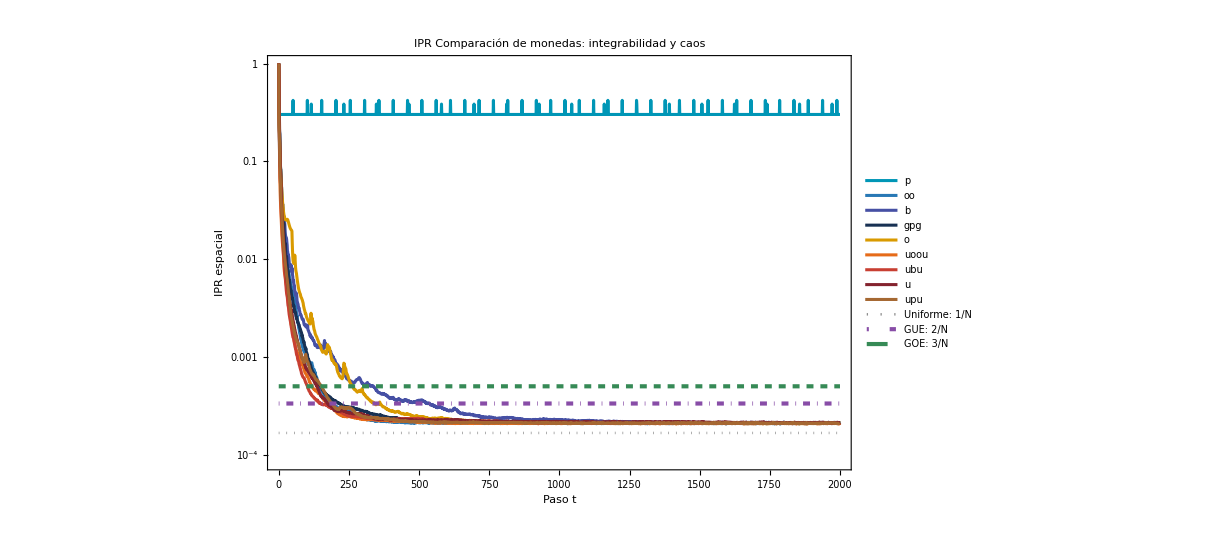

```mathematica
(*Clasificación:integrables hasta "gpg" inclusive*)cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]   (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]   (*upu:cobre*)};
(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias horizontales:1/N,2/N y 3/N*)
referenceValues={1/nSites,2/nSites,3/nSites};

references=Table[{{0,value},{Tmax,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo.Se supone que cada curva de iprDat contiene puntos {t,IPR}.*)
tInset=0.75 Tmax;

lateData=Select[#,First[#]>=tInset&]&/@iprDat;

lateReferences=Table[{{tInset,value},{Tmax,value}},{value,referenceValues}];

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{All,{0.00015,0.00035}},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->35];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],{"Uniforme: 1/N","GUE: 2/N","GOE: 3/N"},LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprDat,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR espacial"},PlotLabel->"IPR\nComparación de monedas: integrabilidad y caos",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.7,0.6}],Center,Scaled[{0.35,0.35}]]}],Placed[legend,Right]]
```

```mathematica
Export["/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/IPR_CompCoins_Localized_Sinai.pdf",Img]
```

/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/IPR_CompCoins_Localized_Sinai.pdf

#### Para estados deslocalizados

Para dimensiones comparables con el sinai

```mathematica
L1=140;R1=100;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

Las dimensiones del rectangulo serían:Lx= 80, Ly= 50

```mathematica
(*Malla y estado inicial*)
Lx=140;
Ly=100;
grid=GenerateSinaiBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=RandomDelocalizedState[dim,4,"RandomSeed"->7];

Tmax=2000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
iprDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];
ComputeSpatialIPREvolution[evolutionOp,initialState,Tmax,CoinDimension->4]]&/@names;
```

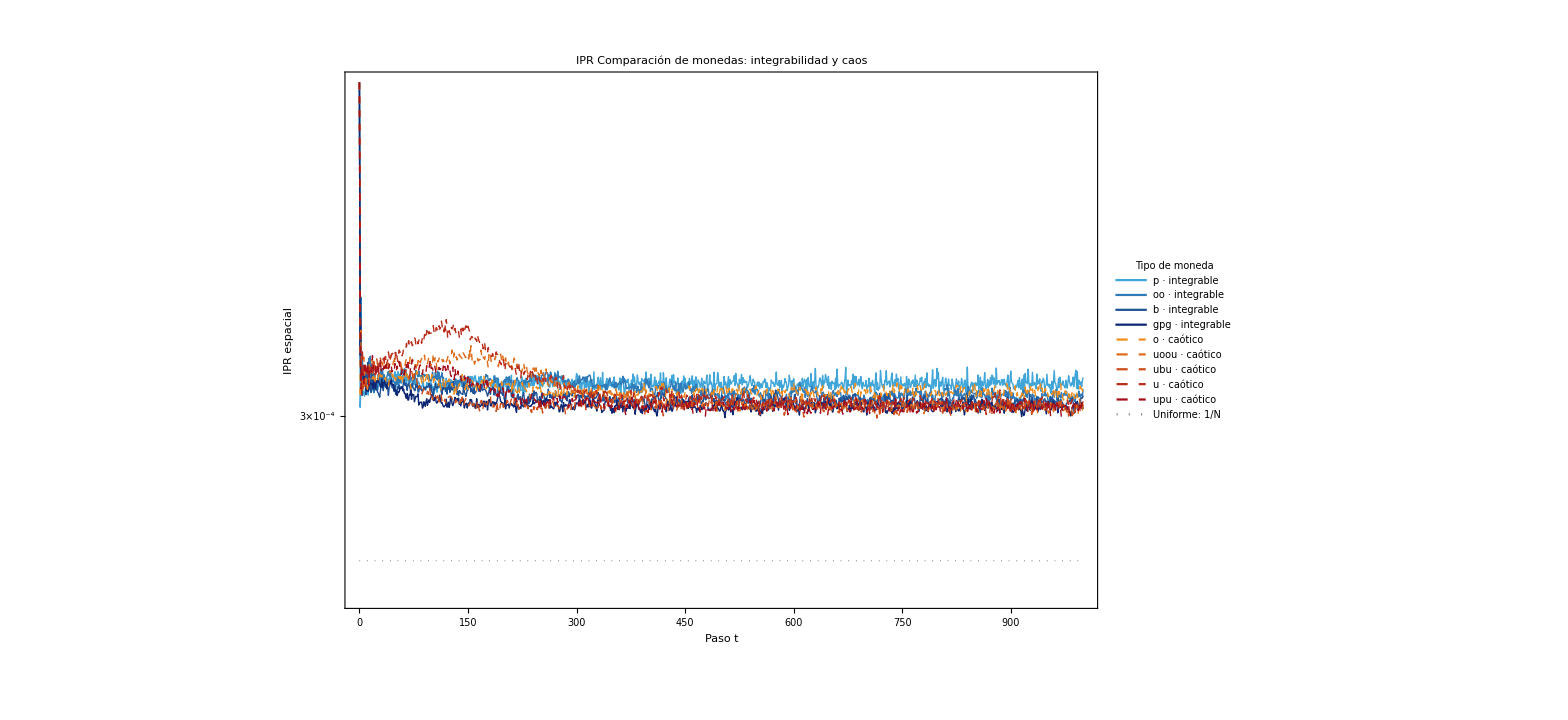

```mathematica
(*Clasificación:integrables hasta "gpg" inclusive*)cut=First[FirstPosition[names,"gpg"]];
nRegular=cut;
nChaotic=Length[names]-cut;

(*Colores individuales*)
regularColors={RGBColor["#0096B6"],(*p:turquesa*)RGBColor["#2878B5"],(*oo:azul*)RGBColor["#4650A4"],(*b:índigo*)RGBColor["#183153"]   (*gpg:azul marino*)};

chaoticColors={RGBColor["#D99A00"],(*o:ocre*)RGBColor["#E66B19"],(*uoou:naranja*)RGBColor["#C83F32"],(*ubu:rojo*)RGBColor["#84232E"],(*u:granate*)RGBColor["#A56832"]   (*upu:cobre*)};
(*Estilos de curvas y referencias*)
styles=Join[Directive[#,AbsoluteThickness[2.2]]&/@regularColors,Directive[#,AbsoluteThickness[2.2]]&/@chaoticColors,{Directive[GrayLevel[0.55],AbsoluteThickness[1.8],Dotted],Directive[RGBColor["#884DA7"],AbsoluteThickness[3],DotDashed],Directive[RGBColor["#368A56"],AbsoluteThickness[3],Dashed]}];

(*Referencias horizontales:1/N,2/N y 3/N*)
referenceValues={1/nSites,2/nSites,3/nSites};

references=Table[{{0,value},{Tmax,value}},{value,referenceValues}];

(*Inset:último 25 % del tiempo.Se supone que cada curva de iprDat contiene puntos {t,IPR}.*)
tInset=0.75 Tmax;

lateData=Select[#,First[#]>=tInset&]&/@iprDat;

lateReferences=Table[{{tInset,value},{Tmax,value}},{value,referenceValues}];

latePlot=ListLinePlot[Join[lateData,lateReferences],PlotStyle->styles,ScalingFunctions->{None,"Log"},PlotRange->{All,{0.00015,0.0006}},Frame->True,Axes->False,LabelStyle->Directive[Black,9],Background->White,ImagePadding->35];

(*Leyenda agrupada*)
legend=Framed[Column[{Grid[{{Column[{Style["Integrables",14,Bold,RGBColor["#183153"]],LineLegend[Take[styles,cut],Take[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7],Column[{Style["Caóticas",14,Bold,RGBColor["#84232E"]],LineLegend[Take[styles,{cut+1,Length[names]}],Drop[names,cut],LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->0.7]}},Alignment->Top,Spacings->{2,0}],Style["Referencias",14,Bold,GrayLevel[0.25]],LineLegend[Take[styles,-3],{"Uniforme: 1/N","GUE: 2/N","GOE: 3/N"},LegendLayout->"Column",LegendMarkerSize->{34,12},LabelStyle->Directive[12]]},Spacings->1],Background->White,FrameStyle->GrayLevel[0.85],FrameMargins->12,RoundingRadius->5];

(*Gráfico final*)
Img=Legended[ListLinePlot[Join[iprDat,references],PlotStyle->styles,ScalingFunctions->{None,"Log"},Frame->True,Axes->False,FrameLabel->{"Paso t","IPR espacial"},PlotLabel->"IPR\nComparación de monedas: integrabilidad y caos",GridLines->Automatic,PlotRange->All,ImageSize->900,LabelStyle->Directive[Bold,17],Epilog->{Inset[latePlot,Scaled[{0.6,0.75}],Center,Scaled[{0.35,0.35}]]}],Placed[legend,Right]]
```

```mathematica
Export["/Users/saul/Desktop/ChatGPT/QWProgramming/Imgs/IPR_CompCoins_DeLocalized_Sinai.pdf",Img]
```

### Densidad de IPR (Matrices Grandes)

#### Para eigenestados alrededor de un valor dado

Veamos la DoS y ver si cambio mucho con el tamaño

```mathematica
Lx=30;
Ly=30;
grid=GenerateRectangleBasis[Lx,Ly];

(*grid debe ser la malla del estadio*)
coinMatrix=N[RandomMatrix["upu"]];

S=BuildShiftOperators[grid,CoinDimension->4];

U=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinMatrix]];
eigenvals=U//Eigenvalues;
eigenphases=Arg[eigenvals];

Histogram[eigenphases,Automatic,"PDF"]
```

Eigenvalues::arh: Because finding 3844 out of the 3844 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

-Graphics-

```mathematica
Lx=80;
Ly=60;
grid=GenerateRectangleBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["b"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinMatrix]]];

(*Parámetros ajustables*)
k=10;
columns=3;
epsilon0=0.4;

sigma=1.001 Exp[-I epsilon0];

(*Ajustar la base de Arnoldi al número solicitado*)
basisSize=Min[Length[U],Max[60,2 k+10]];

{eigenvalues,eigenvectors}=Eigensystem[U,-k,Method->{"Arnoldi","Shift"->sigma,"BasisSize"->basisSize,"MaxIterations"->5000,"Tolerance"->10^-10}];

eigenvectors=Normalize/@eigenvectors;
eigenphases=-Arg[eigenvalues];

(*Ordenar por eigenfase*)
order=Ordering[eigenphases];
eigenvalues=eigenvalues[[order]];
eigenvectors=eigenvectors[[order]];
eigenphases=eigenphases[[order]];

residuals=MapThread[Norm[U.#2-#1 #2]&,{eigenvalues,eigenvectors}];

nFound=Length[eigenvectors];

densities=ComputeSpatialIPRDensity[#,4]&/@eigenvectors;
iprValues=Total/@densities;

(*Resumen*)
summary=Grid[Prepend[Table[{j,NumberForm[eigenphases[[j]],{6,4}],ScientificForm[residuals[[j]],3],ScientificForm[iprValues[[j]],3]},{j,nFound}],{"Estado","ε","Residuo","IPR"}],Frame->All];

(*Un panel por eigenestado*)
plots=Table[DiscreteProbabilityPlot[grid,densities[[j]],"ProbabilityScale"->"Linear",PlotLabel->Column[{Row[{"Estado ",j,"; ε = ",NumberForm[eigenphases[[j]],{6,4}]}],Row[{"IPR = ",ScientificForm[iprValues[[j]],3]}]},Alignment->Center],ImageSize->350],{j,nFound}];

(*Completar únicamente los espacios vacíos de la última fila*)
rows=Ceiling[nFound/columns];

Column[{summary,GraphicsGrid[Partition[PadRight[plots,rows columns,Null],columns],Spacings->{0.4,0.6},ImageSize->400 columns]}]

GraphicsGrid[Partition[PadRight[plots,6,Null],3],Spacings->{0.4,0.6},ImageSize->1200]
```

Estado | ε | Residuo | IPR
1 | 0.3979 | 3.74×10^-14 | 2.92×10^-4
2 | 0.3980 | 3.92×10^-14 | 2.61×10^-4
3 | 0.3983 | 4.15×10^-14 | 2.61×10^-4
4 | 0.3987 | 4.58×10^-14 | 2.97×10^-4
5 | 0.3997 | 3.74×10^-14 | 2.72×10^-4
6 | 0.4002 | 3.29×10^-14 | 3.22×10^-4
7 | 0.4013 | 3.56×10^-14 | 2.99×10^-4
8 | 0.4016 | 3.64×10^-14 | 3.1×10^-4
9 | 0.4018 | 4.21×10^-14 | 2.6×10^-4
10 | 0.4021 | 3.65×10^-14 | 3.11×10^-4
-Graphics-

-Graphics-

#### Tomando eigenestados en puntos distintos del espectro de energías

```mathematica
(*Malla y operador de evolución*)
Lx=100;
Ly=75;
grid=GenerateSinaiBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["oo"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinMatrix]]];

(*Seis intervalos y sus centros*)
k=10;
edges=Subdivide[-Pi,Pi,k];
intervals=Partition[edges,2,1];
targets=Mean/@intervals;

(*Un eigenestado próximo al centro de cada intervalo*)
eigenData=Table[Module[{sigma,vals,vecs,psi,phase,residual},sigma=1.001 Exp[-I targets[[j]]];
{vals,vecs}=Check[Eigensystem[U,-1,Method->{"Arnoldi","Shift"->sigma,"BasisSize"->60,"MaxIterations"->5000,"Tolerance"->10^-10}],Print["No convergió la búsqueda del intervalo ",j];
Abort[]];
psi=Normalize[First[vecs]];
phase=-Arg[First[vals]];
residual=Norm[U.psi-First[vals] psi];
(*No asignar a un intervalo un estado que quedó fuera*)If[!TrueQ[intervals[[j,1]]<=phase<=intervals[[j,2]]],Print["El eigenestado encontrado para el intervalo ",j," quedó fuera: ε = ",phase,". Revisa la búsqueda o si hay espectro en ese intervalo."];
Abort[]];
If[residual>10^-8,Print["Residuo demasiado grande en el intervalo ",j,": ",residual];
Abort[]];
{First[vals],psi,phase,residual}],{j,k}];

eigenvalues=eigenData[[All,1]];
eigenvectors=eigenData[[All,2]];
eigenphases=eigenData[[All,3]];
residuals=eigenData[[All,4]];

densities=ComputeSpatialIPRDensity[#,4]&/@eigenvectors;
iprValues=Total/@densities;

(*Resumen:objetivo,eigenfase encontrada,residuo e IPR*)
summary=Grid[Prepend[Table[{j,NumberForm[N[targets[[j]]],{6,4}],NumberForm[eigenphases[[j]],{6,4}],ScientificForm[residuals[[j]],3],ScientificForm[iprValues[[j]],3]},{j,k}],{"Intervalo","ε objetivo","ε encontrada","Residuo","IPR"}],Frame->All];
(*Configuración de la visualización*)columns=3;
nPlots=Length[eigenvectors];

(*Mapas con títulos externos y leyendas normalizadas*)
plots=Table[Module[{density,dmax,header,graphic},density=densities[[j]];
dmax=Max[density];
header=Row[{"Intervalo ",j,": ",NumberForm[N[intervals[[j,1]]],{4,2}]," a ",NumberForm[N[intervals[[j,2]]],{4,2}]}];
graphic=DiscreteProbabilityPlot[grid,density,"ProbabilityScale"->"Linear","ProbabilityRange"->{0,dmax},ColorFunction->(GrayLevel[1-#]&),PlotLabel->None,FrameLabel->{"x","y"},LabelStyle->Directive[Black,11],ImagePadding->{{45,15},{45,15}},ImageSize->320,PlotLegends->With[{upper=dmax},Placed[BarLegend[{Function[value,GrayLevel[1-Clip[value/upper,{0,1}]]],{0,upper}},LegendLabel->"Iₙ",LegendMarkerSize->{18,180},LabelStyle->Directive[Black,10]],Right]]];
Column[{Style[header,12,Bold],Style[Row[{"ε = ",NumberForm[eigenphases[[j]],{6,4}],"   IPR = ",ScientificForm[iprValues[[j]],3]}],11],Style[Row[{"Residuo = ",ScientificForm[residuals[[j]],2]}],10,GrayLevel[0.35]],graphic},Alignment->Center,Spacings->0.4]],{j,nPlots}];

(*Completar la última fila sin perder paneles*)
panel=Grid[Partition[PadRight[plots,columns Ceiling[nPlots/columns],""],columns],Alignment->{Center,Top},Spacings->{2,2}];

(*Una única imagen con todos los mapas*)
imagen=Rasterize[panel,"Image",ImageResolution->200];

imagen
```

-Graphics-

### Densidad de IPR (Matrices Pequeñas)

```mathematica
(*Malla y operador*)
Lx=60;
Ly=25;
grid=GenerateSinaiBasis[Lx,Ly];

coinMatrix=N[RandomMatrix["b"]];
S=BuildShiftOperators[grid,CoinDimension->4];

U=N[S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinMatrix]]];

(*Espectro completo:eigenvalores y vectores correspondientes*)
{eigenvalues,eigenvectors}=Eigensystem[Normal[U]];
eigenvectors=Normalize/@eigenvectors;
eigenphases=-Arg[eigenvalues];
```

```mathematica
(*Dividir las eigenfases en subintervalos*)
nIntervals=8;
columns=4;

edges=N[Subdivide[-Pi,Pi,nIntervals]];
intervals=Partition[edges,2,1];
centers=Mean/@intervals;

(*Seleccionar un eigenestado cercano al centro de cada intervalo*)
selectedIndices=Table[Module[{candidates},candidates=Select[Range[Length[eigenphases]],Function[index,intervals[[j,1]]<=eigenphases[[index]]&&If[j==nIntervals,eigenphases[[index]]<=intervals[[j,2]],eigenphases[[index]]<intervals[[j,2]]]]];
If[candidates==={},Missing["EmptyInterval"],First[MinimalBy[candidates,Abs[eigenphases[[#]]-centers[[j]]]&]]]],{j,nIntervals}];

(*Construir cada panel*)
plots=Table[Module[{index,density,residual,header,graphic,dmax},index=selectedIndices[[j]];
header=Row[{"Intervalo ",j,": ",NumberForm[intervals[[j,1]],{4,2}]," a ",NumberForm[intervals[[j,2]],{4,2}]}];
If[MissingQ[index],Column[{Style[header,12,Bold],"Sin eigenestados"},Alignment->Center],density=ComputeSpatialIPRDensity[eigenvectors[[index]],4];
dmax=Max[density];
residual=Norm[U.eigenvectors[[index]]-eigenvalues[[index]] eigenvectors[[index]]];
graphic=DiscreteProbabilityPlot[grid,density,"ProbabilityScale"->"Linear","ProbabilityRange"->{0,dmax},ColorFunction->(GrayLevel[1-#]&),PlotLabel->None,FrameLabel->{"x","y"},LabelStyle->Directive[Black,11],ImagePadding->{{45,15},{45,15}},ImageSize->320,(*Leyenda:normalizar la densidad para asignar el color*)PlotLegends->With[{upper=dmax},Placed[BarLegend[{Function[value,GrayLevel[1-Clip[value/upper,{0,1}]]],{0,upper}},LegendLabel->"Iₙ",LegendMarkerSize->{18,180},LabelStyle->Directive[Black,10]],Right]]];
Column[{Style[header,12,Bold],Style[Row[{"ε = ",NumberForm[eigenphases[[index]],{6,4}],"   IPR = ",ScientificForm[Total[density],3]}],11],Style[Row[{"Residuo = ",ScientificForm[residual,2]}],10,GrayLevel[0.35]],graphic},Alignment->Center,Spacings->0.4]]],{j,nIntervals}];

(*Organizar los paneles*)
panel=Grid[Partition[PadRight[plots,columns Ceiling[nIntervals/columns],""],columns],Alignment->{Center,Top},Spacings->{2,2}];

(*Convertir el conjunto en una única imagen*)
imagen=Rasterize[panel,"Image",ImageResolution->200];

imagen
```

R=25

-Graphics-

R=0

-Graphics-

### Tratando de hallar estados de borde mediante a IPR

```mathematica
SeedRandom[23];
Lx=60;
Ly=45;
grid=GenerateSinaiBasis[Lx,Ly];
S=BuildShiftOperators[grid,CoinDimension->4];
nSites=grid["Dimension"];
c=N[RandomMatrix["oo"]];
evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];
(*Eigenvalores y eigenvectores,en el mismo orden*)
{eigenvals,eigenvecs}=Eigensystem[Normal[evolutionOp]];
```

#### IPR vs cuasiEnergías

{-2.82532,-2.82394,-2.82391,-2.82391,-2.82391,-2.82391,-2.82391,-2.82391,-2.82391,-2.82391,-2.82391,-2.82391,-2.8239,-2.8236,-2.82082,-2.47368,-2.42065,-2.31594,-2.27592,-0.190322,-0.0858362,-0.035622,0.314266,0.31734,0.31767,0.317683,0.317684,0.317684,0.317684,0.317684,0.317684,0.317684,0.317684,0.317684,0.317684,0.317713,0.319248,0.64178,0.667737,0.720869,0.825642,2.95132,3.05607}

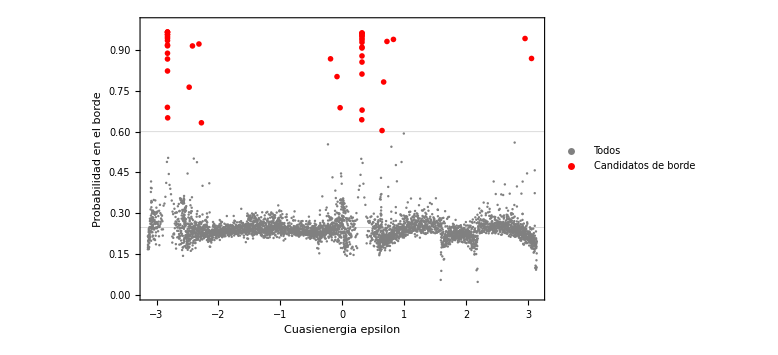

```mathematica
eigenenergies=Arg[eigenvals];
borde=AnalyzeBoundaryEigenstates[grid,eigenvals,eigenvecs,"BoundaryWidth"->2,"BoundaryThreshold"->0.6];

Dataset[borde["Candidates"]]
borde["CandidateEnergies"]
PlotBoundarySpectrum[borde]
```

```mathematica
candidatos=borde["CandidateEnergies"];
imgs=Module[{result},result=EigenstateAtEnergy[candidatos[[#]],eigenvals,eigenvecs];
DiscreteProbabilityPlot[grid,result["State"],"InputType"->"State",PlotLabel->"Desde amplitudes",ImageSize->200]]&/@Range[1,candidatos//Length]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Chequeando Histograma

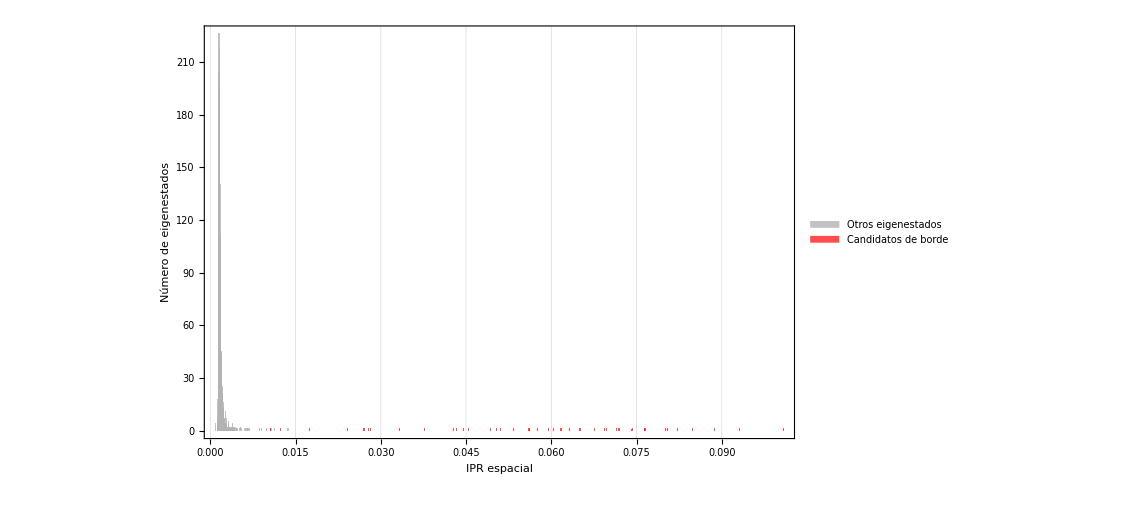

```mathematica
IPRdat=ComputeSpatialIPR[#,4]&/@eigenvecs;

indicesBorde=borde["CandidateIndices"];
indicesOtros=Complement[Range[Length[IPRdat]],indicesBorde];

iprBorde=IPRdat[[indicesBorde]];
iprOtros=IPRdat[[indicesOtros]];

(*Los mismos intervalos del histograma original*)
limites=First[HistogramList[IPRdat,"FreedmanDiaconis"]];
Histogram[{iprOtros,iprBorde},{limites},"Count",ChartLayout->"Stacked",ChartStyle->{Directive[GrayLevel[0.7],EdgeForm[None]],Directive[Red,EdgeForm[None]]},ChartLegends->{"Otros eigenestados","Candidatos de borde"},GridLines->{DeleteDuplicates[iprBorde],None},GridLinesStyle->Directive[Red,Opacity[0.6],Dotted,AbsoluteThickness[1.5]],Frame->True,Axes->False,FrameLabel->{"IPR espacial","Número de eigenestados"},PlotRange->All,ImageSize->Large]
```

## Entropía de entrelazamiento

## Rectangulo

### Un caso particular

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=80;
Ly=50;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=100;
c=N[RandomMatrix["oo"]];
evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];
```

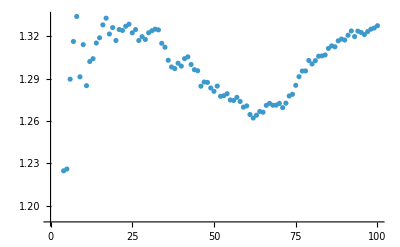

```mathematica
entropyDat1=ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax];
ListPlot[entropyDat1]
```

### Comparando Monedas

#### Para un estado localizado

Para dimensiones comparables con el sinai

```mathematica
L1=120;R1=90;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

Las dimensiones del rectangulo serían:Lx= 80, Ly= 50

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=80;
Ly=50;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=1000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
EntropyDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];
ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax]]&/@names;
```

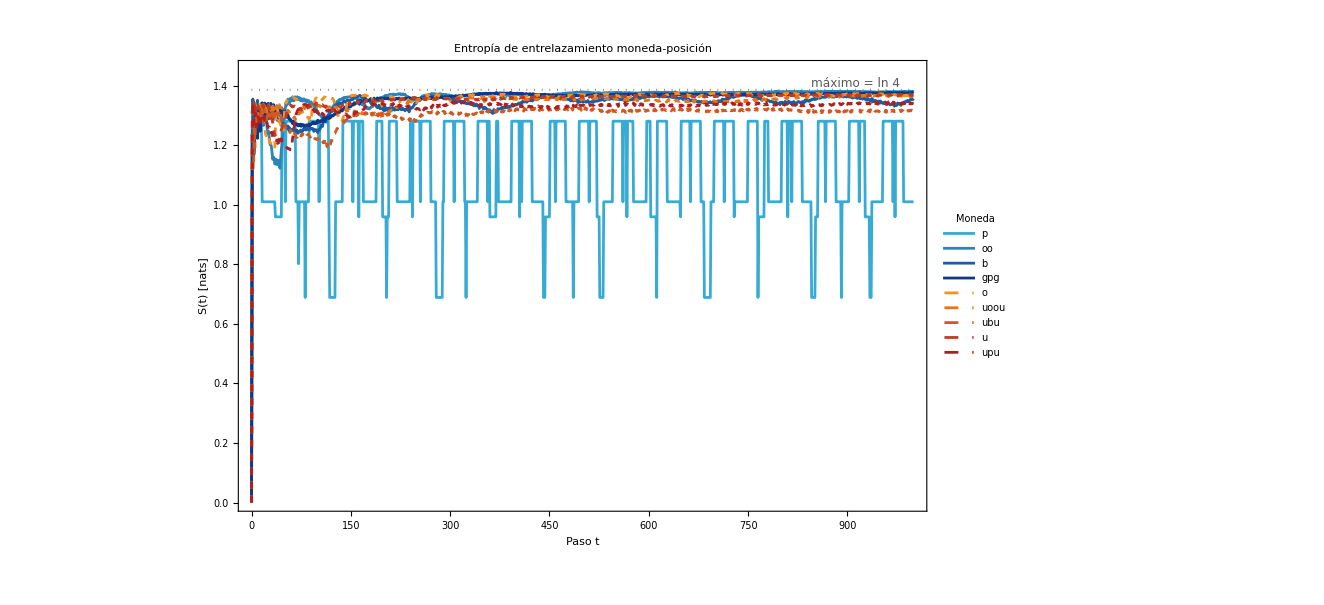
-Graphics-
-Graphics-

```mathematica
PlotEntropiaMonedas[EntropyDat,names,20]
```

#### Para estados deslocalizados

Para dimensiones comparables con el sinai

```mathematica
L1=120;R1=90;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

Las dimensiones del rectangulo serían:Lx= 80, Ly= 50

```mathematica
Lx=80;
Ly=50;
grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=RandomDelocalizedState[dim,4,"RandomSeed"->7];

Tmax=1000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
entropyDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];
ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax]]&/@names;
```

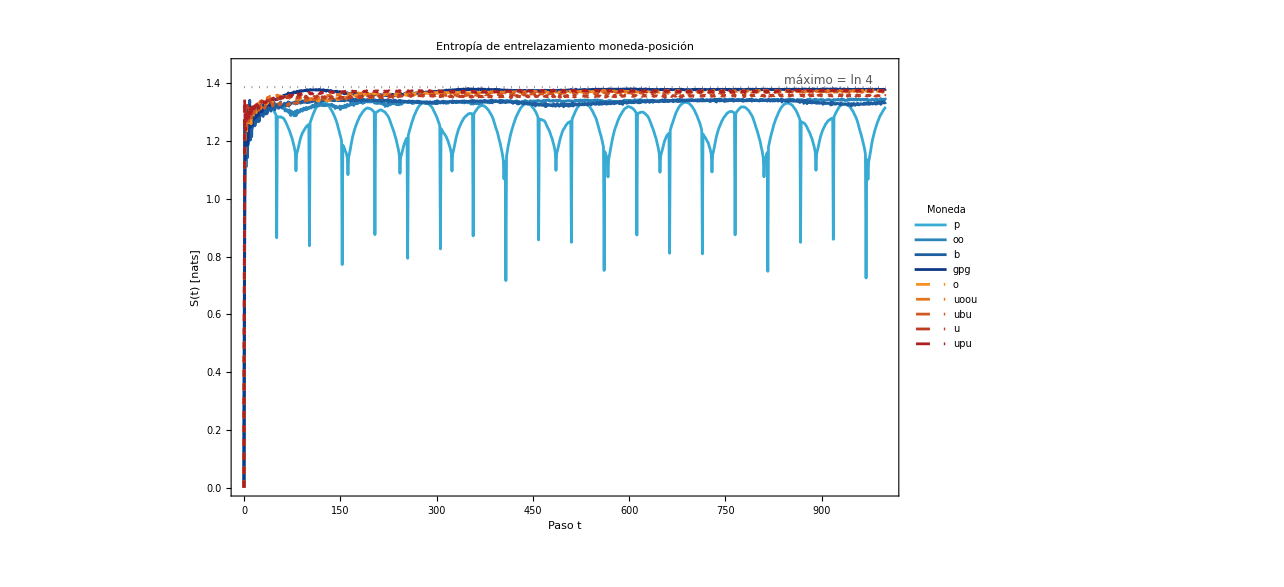
-Graphics-
-Graphics-

```mathematica
PlotEntropiaMonedas[entropyDat,names,20]
```

#### rutina de visualización

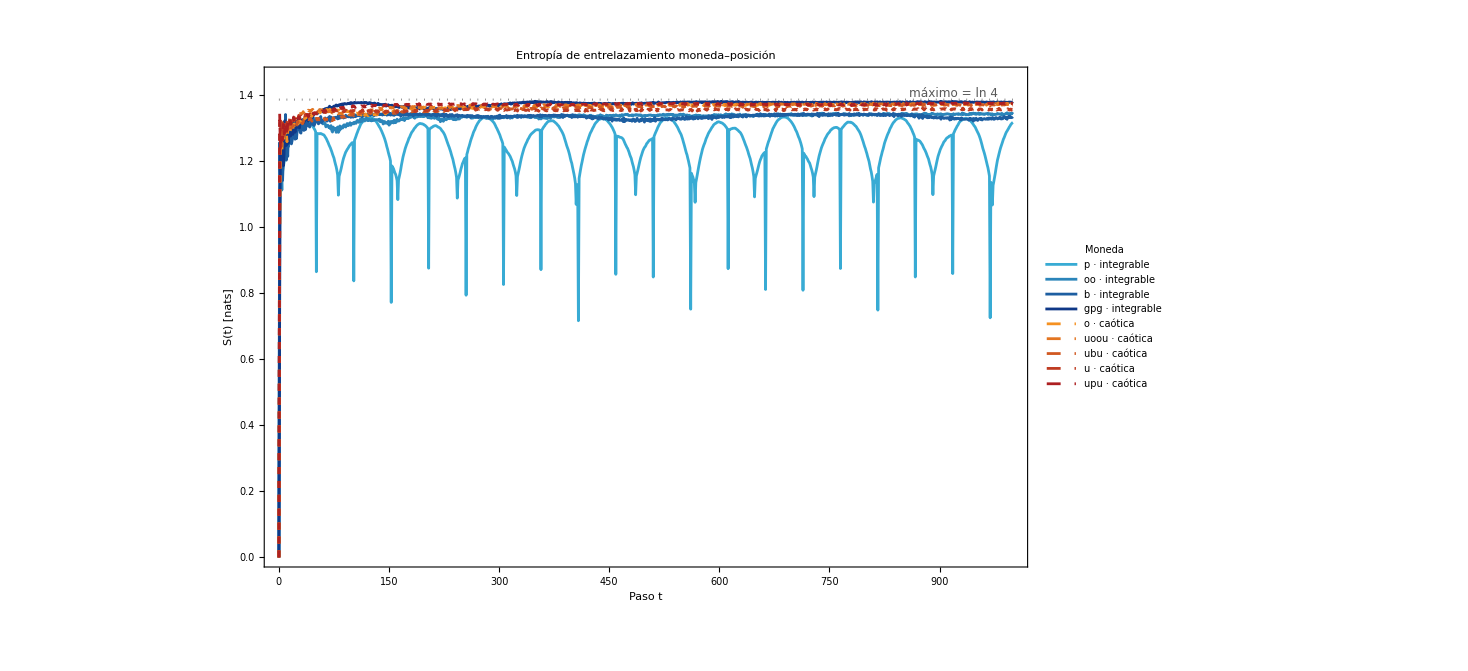
-Graphics-
-Graphics-

```mathematica
(*Entropía de entrelazamiento:vista completa y detalle por grupo*)cut=First@FirstPosition[names,"gpg"];
sMax=Log[4];                 (*Cota para una moneda de dimensión 4*)
tZoom=20;                   (*Inicio de los paneles de detalle*)

palette[endpoints_List,n_Integer]:=Blend[endpoints,#]&/@If[n==1,{0.5},Subdivide[0,1,n-1]];

regularColors=palette[{RGBColor[0.22,0.67,0.83],RGBColor[0.06,0.22,0.53]},cut];

chaoticColors=palette[{RGBColor[0.96,0.57,0.13],RGBColor[0.68,0.12,0.13]},Length[names]-cut];

regularStyles=Directive[#,AbsoluteThickness[2]]&/@regularColors;

chaoticStyles=Directive[#,AbsoluteThickness[2],Dashed]&/@chaoticColors;

styles=Join[regularStyles,chaoticStyles];

labels=Join[(#<>" · integrable"&)/@Take[names,cut],(#<>" · caótica"&)/@Drop[names,cut]];

(*Rango vertical común para ambos acercamientos*)
lateValues=Flatten[entropyDat[[All,tZoom+1;;,2]]];
{yMin,yMax}=MinMax[lateValues];
margin=Max[0.02 sMax,0.12 (yMax-yMin)];
zoomY={Max[0,yMin-margin],Min[1.05 sMax,yMax+margin]};

fullPlot=ListLinePlot[entropyDat,PlotStyle->styles,PlotLegends->Placed[LineLegend[styles,labels,LegendLabel->"Moneda"],Right],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Entropía de entrelazamiento moneda–posición",PlotRange->{{0,Tmax},{0,1.05 sMax}},GridLines->{Automatic,{Log[2]}},GridLinesStyle->Directive[GrayLevel[0.85],Dashed],Epilog->{Directive[GrayLevel[0.4],Dotted,AbsoluteThickness[1.5]],Line[{{0,sMax},{Tmax,sMax}}],Inset[Style["máximo = ln 4",12,GrayLevel[0.35]],{0.98 Tmax,sMax},{Right,Bottom}]},ImageSize->950,LabelStyle->Directive[14]];

regularZoom=ListLinePlot[Take[entropyDat,cut],PlotStyle->regularStyles,PlotLegends->Placed[LineLegend[regularStyles,Take[names,cut]],Below],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Integrables: detalle",PlotRange->{{tZoom,Tmax},zoomY},GridLines->Automatic,ImageSize->460];

chaoticZoom=ListLinePlot[Drop[entropyDat,cut],PlotStyle->chaoticStyles,PlotLegends->Placed[LineLegend[chaoticStyles,Drop[names,cut]],Below],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Caóticas: detalle",PlotRange->{{tZoom,Tmax},zoomY},GridLines->Automatic,ImageSize->460];

Column[{fullPlot,GraphicsRow[{regularZoom,chaoticZoom},Spacings->15]},Center,2]
```

## Sinai

### Un caso particular

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=80;
Ly=50;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=100;
c=N[RandomMatrix["oo"]];
evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];
```

```mathematica
entropyDat1=ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax];
ListPlot[entropyDat1]
```

-Graphics-

### Comparando Monedas

#### Para un estado localizado

Para dimensiones comparables con el sinai

```mathematica
L1=120;R1=90;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

Las dimensiones del rectangulo serían:Lx= 80, Ly= 50

```mathematica
SeedRandom[23];

(*Malla y estado inicial*)
Lx=120;
Ly=90;
grid=GenerateSinaiBasis[Lx,Ly];
pos={105,45};

coin=N[Normalize[HaarRandomState[4]]];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];

Tmax=1000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
EntropyDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];
ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax]]&/@names;
```

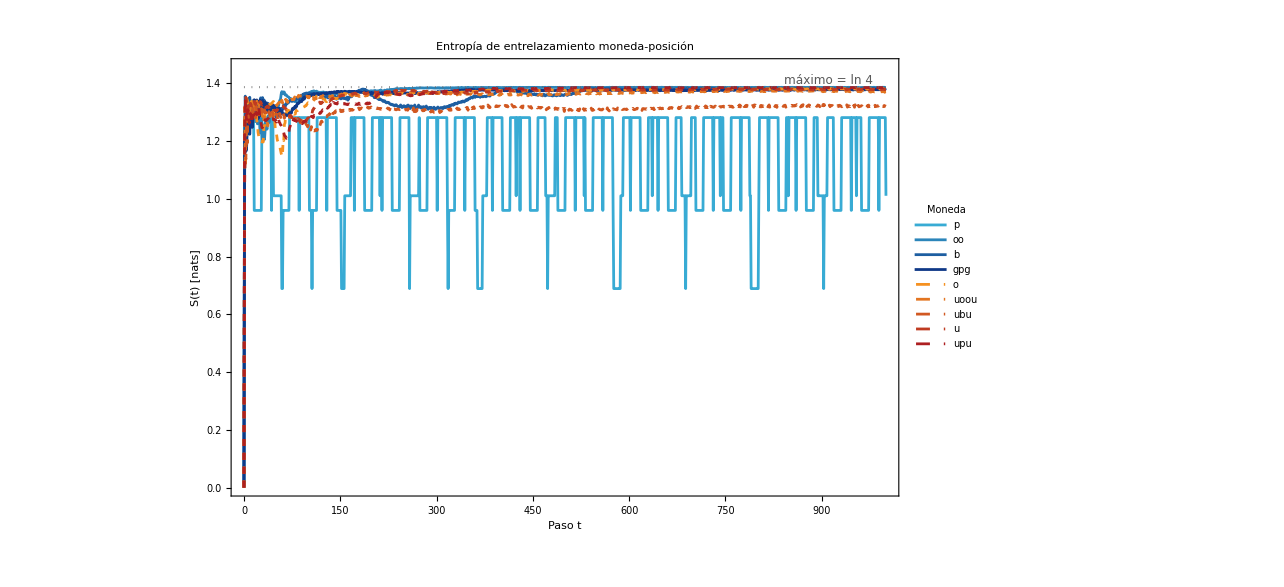
-Graphics-
-Graphics-

```mathematica
PlotEntropiaMonedas[EntropyDat,names,20]
```

#### Para estados deslocalizados

Para dimensiones comparables con el sinai

```mathematica
L1=120;R1=90;
GridDataSinai=GenerateSinaiBasis[L1,R1];
dim=GridDataSinai["Dimension"];
aurea=GoldenRatio//N;
Ly=Floor[Sqrt[dim/aurea]];
Lx=Floor[Ly*aurea];
Print["Las dimensiones del rectangulo serían:","Lx= ",Lx,", Ly= ",Ly]
```

Las dimensiones del rectangulo serían:Lx= 80, Ly= 50

```mathematica
Lx=120;
Ly=90;
grid=GenerateSinaiBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=RandomDelocalizedState[dim,4,"RandomSeed"->7];

Tmax=1000;
nSites=grid["Dimension"];
names=RandomMatrixNames[];

(*Evolución de la IPR para cada tipo de moneda*)
entropyDat=Module[{c=N[RandomMatrix[#]],evolutionOp},evolutionOp=S.KroneckerProduct[IdentityMatrix[nSites,SparseArray],SparseArray[c]];
ComputeEntanglementEntropyEvolution[evolutionOp,initialState,Tmax]]&/@names;
```

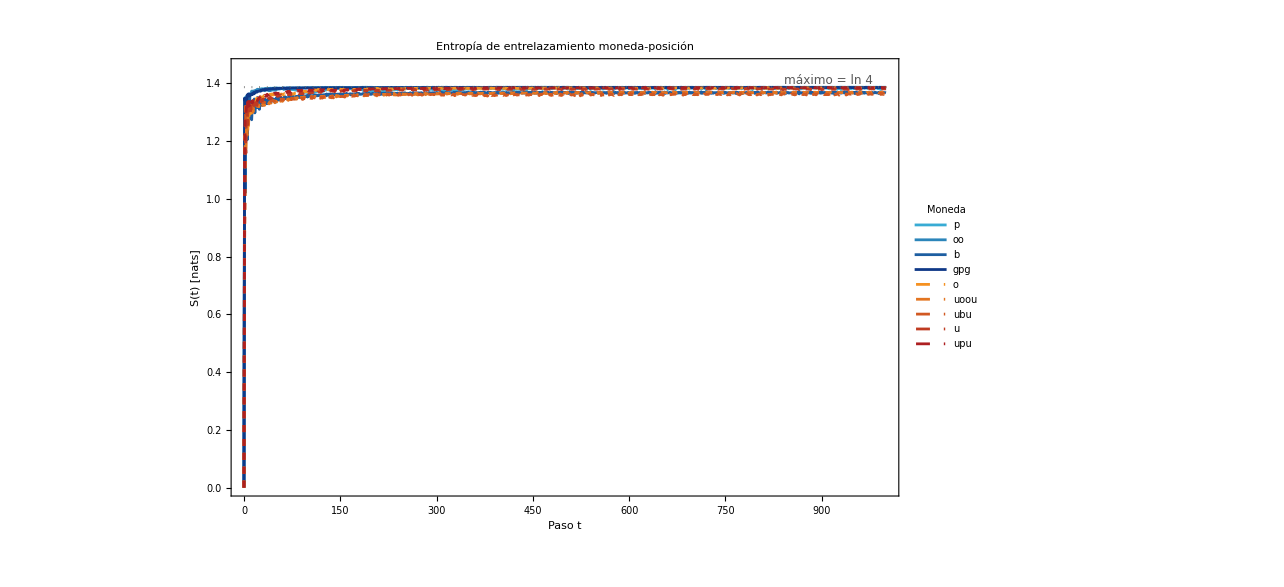
-Graphics-
-Graphics-

```mathematica
PlotEntropiaMonedas[entropyDat,names,20]
```

#### rutina de visualización

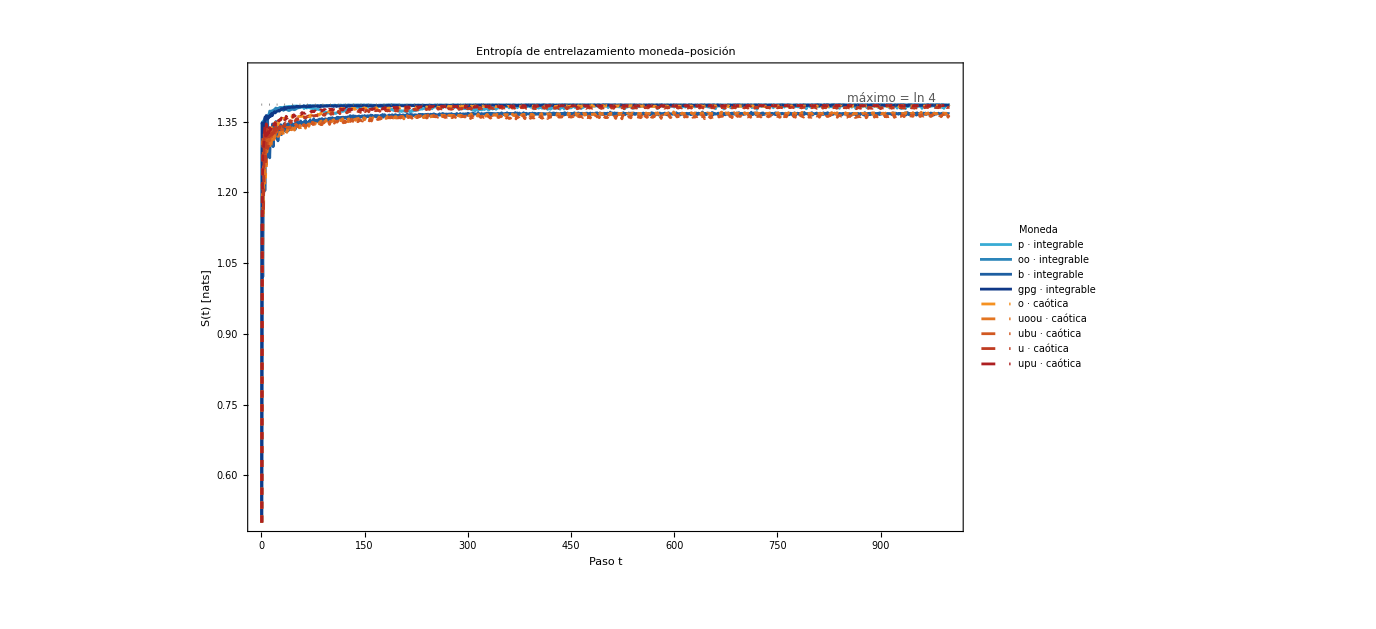
-Graphics-
-Graphics-

```mathematica
(*Entropía de entrelazamiento:vista completa y detalle por grupo*)cut=First@FirstPosition[names,"gpg"];
sMax=Log[4];                 (*Cota para una moneda de dimensión 4*)
tZoom=20;                   (*Inicio de los paneles de detalle*)

palette[endpoints_List,n_Integer]:=Blend[endpoints,#]&/@If[n==1,{0.5},Subdivide[0,1,n-1]];

regularColors=palette[{RGBColor[0.22,0.67,0.83],RGBColor[0.06,0.22,0.53]},cut];

chaoticColors=palette[{RGBColor[0.96,0.57,0.13],RGBColor[0.68,0.12,0.13]},Length[names]-cut];

regularStyles=Directive[#,AbsoluteThickness[2]]&/@regularColors;

chaoticStyles=Directive[#,AbsoluteThickness[2],Dashed]&/@chaoticColors;

styles=Join[regularStyles,chaoticStyles];

labels=Join[(#<>" · integrable"&)/@Take[names,cut],(#<>" · caótica"&)/@Drop[names,cut]];

(*Rango vertical común para ambos acercamientos*)
lateValues=Flatten[entropyDat[[All,tZoom+1;;,2]]];
{yMin,yMax}=MinMax[lateValues];
margin=Max[0.02 sMax,0.12 (yMax-yMin)];
zoomY={Max[0,yMin-margin],Min[1.05 sMax,yMax+margin]};

fullPlot=ListLinePlot[entropyDat,PlotStyle->styles,PlotLegends->Placed[LineLegend[styles,labels,LegendLabel->"Moneda"],Right],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Entropía de entrelazamiento moneda–posición",PlotRange->{{0,Tmax},{0.5,1.05 sMax}},GridLines->{Automatic,{Log[2]}},GridLinesStyle->Directive[GrayLevel[0.85],Dashed],Epilog->{Directive[GrayLevel[0.4],Dotted,AbsoluteThickness[1.5]],Line[{{0,sMax},{Tmax,sMax}}],Inset[Style["máximo = ln 4",12,GrayLevel[0.35]],{0.98 Tmax,sMax},{Right,Bottom}]},ImageSize->950,LabelStyle->Directive[14]];

regularZoom=ListLinePlot[Take[entropyDat,cut],PlotStyle->regularStyles,PlotLegends->Placed[LineLegend[regularStyles,Take[names,cut]],Below],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Integrables: detalle",PlotRange->{{tZoom,Tmax},zoomY},GridLines->Automatic,ImageSize->460];

chaoticZoom=ListLinePlot[Drop[entropyDat,cut],PlotStyle->chaoticStyles,PlotLegends->Placed[LineLegend[chaoticStyles,Drop[names,cut]],Below],ScalingFunctions->None,Frame->True,Axes->False,FrameLabel->{"Paso t","S(t) [nats]"},PlotLabel->"Caóticas: detalle",PlotRange->{{tZoom,Tmax},zoomY},GridLines->Automatic,ImageSize->460];

Column[{fullPlot,GraphicsRow[{regularZoom,chaoticZoom},Spacings->15]},Center,2]
```

## Estadística Espectral

## Rectángulo

### Para un caso particular

```mathematica
coinDiag=DiagonalMatrix[Exp[I({0.1,0.2,0.3,0.4}+1)]];
v=RandomVariate[CircularOrthogonalMatrixDistribution[4]];
coinOp=v.coinDiag.ConjugateTranspose[v];
```

```mathematica
Ly=20;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=coinOp;
EvolOp=S.KroneckerProduct[IdentityMatrix[dim,SparseArray],c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=Arg[eigenvals];
```

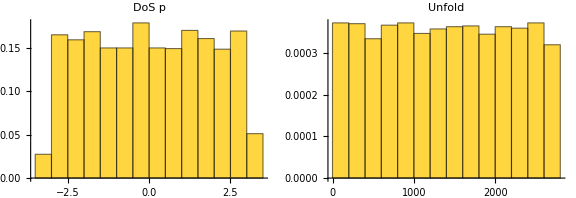

```mathematica
GraphicsRow[{Histogram[eigenphases,Automatic,"PDF",PlotLabel->"DoS\n"<>RandomMatrixNames[][[1]]],Histogram[UnfoldCircular[eigenphases]["UnfoldedLevels"],Automatic,"PDF",PlotLabel->"Unfold"]},ImageSize->Large]
```

#### Ps

```mathematica
QWPs[eigenphases]
```

QWPs::badUnfold: UnfoldCircular no produjo niveles circulares válidos; revisa las fases y el ajuste de Fourier.

$Failed

Por si hay muchas degeneracione, rutina a mano

```mathematica
unfold=UnfoldCircular[eigenphases]["UnfoldedLevels"];
spacings=Differences[unfold//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, Automatic, "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

-Graphics-

#### P(r)

```mathematica
QWPr[eigenphases]
```

QWPr::badSpacings: Las fases deben ser distintas módulo 2 Pi para calcular los cocientes de espaciamientos circulares.

$Failed

```mathematica
u=UnfoldCircular[eigenphases];
orden=Ordering[Mod[N[eigenphases]+Pi,2 Pi]];
niveles=N[u["UnfoldedLevels"]][[orden]];
sPs=Differences[Append[niveles,First[niveles]+Length[niveles]]];

angulos=Sort[Mod[N[eigenphases]+Pi,2 Pi]];
sPr=Differences[Append[angulos,First[angulos]+2 Pi]];

<|"Espaciamientos P(s) no positivos"->Count[sPs,x_/;x<=0],"Espaciamientos P(r) no positivos"->Count[sPr,x_/;x<=0],"Espaciamientos P(r) casi nulos"->Count[sPr,x_/;x<=10^-12]|>
```

<|Espaciamientos P(s) no positivos→1506,Espaciamientos P(r) no positivos→1296,Espaciamientos P(r) casi nulos→2664|>

### Para un caso particular

```mathematica
coinDiag=DiagonalMatrix[{0.1,0.2,0.3,0.4}];
v=RandomVariate[CircularOrthogonalMatrixDistribution[4]];
coinOp=v.coinDiag.ConjugateTranspose[v];
```

```mathematica
Ly=25;Lx=45;
GridData=GenerateSinaiBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=coinOp;
EvolOp=S.KroneckerProduct[IdentityMatrix[dim,SparseArray],c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=Arg[eigenvals];
```

```mathematica
GraphicsRow[{Histogram[eigenphases,Automatic,"PDF",PlotLabel->"DoS\n"<>RandomMatrixNames[][[1]]],Histogram[UnfoldCircular[eigenphases]["UnfoldedLevels"],Automatic,"PDF",PlotLabel->"Unfold"]},ImageSize->Large]
```

-Graphics-

#### Ps

```mathematica
QWPs[eigenphases]
```

QWPs::badUnfold: UnfoldCircular no produjo niveles circulares válidos; revisa las fases y el ajuste de Fourier.

$Failed

Por si hay muchas degeneracione, rutina a mano

```mathematica
unfold=UnfoldCircular[eigenphases]["UnfoldedLevels"];
spacings=Differences[unfold//Sort,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, Automatic, "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Img=Show[EmpiricalHistogram,TheoreticalCurves]
```

-Graphics-

#### P(r)

```mathematica
QWPr[eigenphases]
```

QWPr::badSpacings: Las fases deben ser distintas módulo 2 Pi para calcular los cocientes de espaciamientos circulares.

$Failed

```mathematica
u=UnfoldCircular[eigenphases];
orden=Ordering[Mod[N[eigenphases]+Pi,2 Pi]];
niveles=N[u["UnfoldedLevels"]][[orden]];
sPs=Differences[Append[niveles,First[niveles]+Length[niveles]]];

angulos=Sort[Mod[N[eigenphases]+Pi,2 Pi]];
sPr=Differences[Append[angulos,First[angulos]+2 Pi]];

<|"Espaciamientos P(s) no positivos"->Count[sPs,x_/;x<=0],"Espaciamientos P(r) no positivos"->Count[sPr,x_/;x<=0],"Espaciamientos P(r) casi nulos"->Count[sPr,x_/;x<=10^-12]|>
```

<|Espaciamientos P(s) no positivos→1506,Espaciamientos P(r) no positivos→1296,Espaciamientos P(r) casi nulos→2664|>

### Para calcular un monton de monedas

Primero la data

```mathematica
Ly=20;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
```

### DoS

```mathematica
GraphicsRow[{Histogram[eigenvalData[[#]],Automatic,"PDF",PlotLabel->"DoS\n"<>RandomMatrixNames[][[#]]],Histogram[UnfoldCircular[eigenvalData[[#]]]["UnfoldedLevels"],Automatic,"PDF",PlotLabel->"Unfold"]},ImageSize->Large]&/@Range[RandomMatrixNames[]//Length]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### P(s)

```mathematica
QWPs[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

QWPs::badUnfold: UnfoldCircular no produjo niveles circulares válidos; revisa las fases y el ajuste de Fourier.

{$Failed,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### SFF

```mathematica
QWSFF[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### P(r)

```mathematica
QWPr[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

{$Failed,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### P(s)

#### Un solo caso

```mathematica
Ly=25;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
c=RandomMatrix["o"]//N;
S=BuildShiftOperators[GridData,CoinDimension->4];
EvolOp=S.KroneckerProduct[IdentityMatrix[dim,SparseArray],c];
eigenvals=EvolOp//Eigenvalues;
eigenphases=Arg[eigenvals];
```

Eigenvalues::arh: Because finding 4264 out of the 4264 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

```mathematica
QWPs[eigenphases]
QWSFF[eigenphases]
QWPr[eigenphases]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
?QWSpectralData
```

```mathematica
QWSpectralData[GridData,c]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Viendo todas las monedas

```mathematica
Ly=19;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
c=RandomMatrix["o"]//N;
S=BuildShiftOperators[GridData,CoinDimension->4];
```

```mathematica
test=Module[{c=RandomMatrix["o"]//N,EvolOp,eigenvals,eigenphases},
EvolOp=S.KroneckerProduct[IdentityMatrix[dim,SparseArray],c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=Arg[eigenvals]];
```

```mathematica
QWPs[test,PlotLabel->"o"]
```

QWPs[{1.35968,-1.99087,0.769692,1.08001,1.13809,0.982214,-1.29738,-2.72112,-2.60668,-2.69418,-2.04573,-0.800785,2.06637,0.318111,2.15799,-0.18529,0.113655,-0.799435,1.83688,1.08512,0.914972,2.824,-1.22611,-0.261415,-1.83757,0.438601,-1.86892,1.22351,2.15797,0.961942,-0.433994,-1.97097,-0.138736,-1.88359,-2.08676,1.20816,1.04159,0.0832133,2.06637,-2.00031,1.051,-2.02641,1.04683,0.317919,-1.84373,1.30407,-1.9968,-1.05428,-0.320622,-1.74434,1.57294,0.253031,2.74718,1.44584,0.721995,-2.09089,1.70615,-0.804595,0.436009,1.16567,1.16469,0.923124,0.323943,0.0616408,-3.0215,1.48777,-1.32667,-2.74813,-1.992,1.70204,0.925537,0.00400409,2.04363,-1.84923,-3.10252,-0.995549,0.921379,-1.93424,-1.70602,1.43442,0.462674,0.282772,3.10541,-3.08485,-2.83518,2.17755,1.92765,1.68437,-1.43881,0.487621,-2.04791,-1.94567,0.728923,2.00033,1.38256,-1.31732,1.20963,1.15634,0.429028,-2.6682,-2.53464,-1.96471,1.3915,1.3296,1.19708,1.15247,2.13244,1.74499,-1.55543,-1.33681,-1.26073,-0.219919,1.18332,0.219407,3.08153,-2.64943,1.05278,1.04286,0.118987,-2.58386,1.89328,-1.88838,-1.81372,1.28784,-1.25456,-1.21605,0.526742,0.440201,1.95016,3.09793,-2.85718,2.21297,-2.15757,-1.90176,-0.895619,0.469868,-3.1405,-2.83947,-1.93227,-1.30935,0.592275,-2.92851,-2.90039,-2.79638,1.91648,1.801,-1.7705,-1.43254,-0.0381951,-0.0332171,-2.4096,-1.41897,1.23683,-1.21922,-2.2341,-1.98278,-1.75106,1.70105,1.6125,0.915247,0.846089,-0.807136,-0.802483,-2.7456,-1.85805,1.49288,-1.43183,-0.330251,0.0339285,2.28875,-2.24429,-1.94683,-1.79124,-2.80209,2.69546,1.19437,1.04041,-0.919744,0.744526,0.67219,-2.69548,-2.31118,1.55609,-1.29544,-0.267934,-0.11667,0.0258737,2.96857,-2.85175,2.68212,-2.02544,1.9839,-1.28457,3.10811,1.76799,0.698712,0.505983,-3.10324,2.92118,-1.88529,1.18587,-0.92231,0.825521,-0.414878,0.0821274,-1.95888,-1.80724,0.507684,2.84144,2.24108,2.22418,2.20555,1.70347,1.70073,-1.08236,0.467876,0.106409,-2.93164,-2.60769,2.22207,2.01138,1.68188,1.16134,0.989038,0.417252,1.96455,1.61511,-1.5244,1.42905,1.33343,-1.2784,1.09646,-0.839423,0.7685,-0.120199,2.80153,-2.62337,-2.15965,-1.48771,0.324521,-0.251437,-2.88096,2.83555,-2.82033,-2.25922,-2.06374,-1.78275,1.66222,-1.52868,-1.45847,1.44234,1.23854,-2.89782,2.71677,-2.37579,2.13983,-1.94075,1.84059,-1.79375,1.05412,1.00731,0.583008,0.5442,-0.307573,0.241409,0.177405,-3.03805,-2.05969,-2.05382,-2.02096,-1.95382,1.84825,-1.73475,1.08779,0.913651,-0.842367,0.396673,-0.296565,3.06398,-1.97978,-1.83325,1.59668,1.47342,0.98606,0.844735,0.487899,0.0364332,-2.97258,-2.90759,-2.82248,2.79072,2.7355,2.72425,-2.48189,-1.91496,1.32595,-1.13713,0.250556,2.84746,-2.59861,-1.77524,1.20685,1.16031,1.07226,-0.800531,0.580874,0.200166,-0.171603,-2.90198,-2.81535,2.24451,-1.86192,-1.17825,-1.16303,-0.902376,-0.901421,-0.128607,0.122,-0.0987029,3.01214,2.77605,-2.67124,-2.61364,-2.54943,-2.47443,-1.94937,1.59082,-1.51087,1.43373,-1.42176,1.39901,1.11732,0.9376,0.668859,-0.0360396,-2.6714,2.31979,-2.24509,-2.11166,1.9902,-1.82835,1.7274,1.7136,-1.40065,-0.853817,0.835101,0.614772,0.468429,3.09335,-2.60269,-2.27969,-2.05088,-1.97321,-1.81114,1.44074,-1.41292,1.16424,0.664931,0.177705,0.076051,0.0433052,-0.0336916,3.02185,2.71256,-2.45051,-2.28257,-1.95772,-1.88469,1.62401,1.59174,1.51112,1.50736,1.42656,1.36089,1.15987,-0.897187,-0.765887,-0.759981,0.621904,0.416601,-0.363217,-0.342936,-3.04047,2.72868,-2.68561,2.14195,-1.97913,1.96528,-1.91587,-1.56891,-1.11936,0.964273,0.621217,-0.349149,-0.187004,0.0971932,-3.0227,-2.22132,-2.03851,-1.43565,1.32236,1.02832,0.933849,0.743251,0.101898,2.85012,-2.54703,2.2452,2.23985,-1.62572,1.44669,1.29143,0.907968,0.900818,0.406895,-0.352746,-0.0450448,3.02857,2.98579,-2.91307,-2.81019,-2.46923,2.406,2.31832,-2.19,-1.93361,-1.89662,-1.74266,1.7126,1.49487,1.41466,1.11435,0.786456,0.527914,0.27461,0.0501913,-2.75009,-2.6677,-2.50503,2.34423,-2.12617,2.09112,-1.96799,1.62887,1.61684,-1.17771,-1.15253,0.94246,0.915527,0.858284,-0.816104,0.662566,0.641243,0.42323,0.349673,0.304458,-0.239025,-0.0100505,0.00381419,3.04863,-2.85832,-2.10055,-2.09246,1.9107,-1.83957,1.83783,1.65982,-1.57534,1.24308,0.784301,3.05452,-2.86868,-2.70395,2.11204,1.86288,-1.81913,1.67029,1.65355,-1.48275,-1.12872,0.939193,-0.313684,0.301691,0.239582,3.08896,-3.05832,-1.95538,-1.80544,1.75698,1.7033,-1.52248,-1.48545,-1.21152,1.17792,0.928018,0.713151,0.464628,-0.0443379,-2.37787,2.27192,2.18509,-1.81052,1.76171,1.53704,-1.42489,1.36585,1.32362,-0.797306,0.771146,0.748382,-0.700765,0.536496,0.411298,0.358551,-0.332376,0.288632,0.244224,-0.120778,-3.13362,-3.08813,3.07808,3.03415,2.95174,-2.89766,-2.84085,-2.6877,-2.4907,-1.91915,-1.7657,1.70164,-1.47325,1.1729,1.07765,1.06366,0.991388,0.735656,0.638953,0.424945,-0.264884,-0.150413,3.0758,2.93872,-2.81705,-2.45009,2.23376,-1.96972,-1.93819,1.93427,-1.89222,1.84596,-1.80572,-1.76242,1.60927,-1.47506,1.3022,-1.2807,1.17751,1.14782,-0.717076,0.585244,0.479386,0.420411,-0.0491407,3.03263,2.95609,2.84914,-2.70987,-2.42968,2.42358,-2.40551,-2.26829,-2.15616,-2.08313,1.97517,-1.63564,-1.53055,-1.49559,1.46176,-1.39273,-1.14394,1.1334,1.03275,0.965389,0.655805,0.46722,-0.0410356,-3.0936,2.82122,2.72639,-2.5668,2.33143,-2.15189,-2.01424,-1.98628,1.82854,-1.57451,-1.43924,1.37226,-1.30766,0.977511,0.904848,-0.7234,0.693293,0.659512,0.658128,0.414543,0.0587647,2.9044,2.86819,2.83577,2.18955,-2.16562,1.97196,1.68905,-1.62982,0.252388,-0.240272,0.168338,0.0530859,3.00846,-2.49343,-2.00975,-1.97828,-1.96431,-1.90041,-1.81579,1.80188,1.71463,1.58489,1.56364,1.34237,1.33407,1.25694,1.24214,-0.149412,-0.08247,0.0393982,3.08402,-2.8952,2.76389,-2.19019,-2.00548,-1.9023,1.74374,-1.56353,-1.43994,1.18405,-0.934091,0.597943,0.294284,0.087689,3.13367,2.81879,-2.63875,-2.58932,-2.52787,-2.43377,2.41597,2.3409,-2.26348,-2.10989,2.03362,1.97357,1.1708,1.07147,-0.809213,0.800141,-0.785718,-0.305697,-3.0738,3.0096,-3.00942,2.93641,2.92736,-2.81299,2.74051,-2.70218,-2.48826,-2.30023,1.98053,-1.90694,-1.82028,1.74817,-1.4026,-1.19238,-1.13306,-0.836349,-0.805841,0.645253,0.264965,0.228242,0.138812,-0.111619,0.0155845,2.96238,-2.65283,-2.51987,2.26585,2.22981,-2.19619,-2.09967,-2.0896,2.08947,-1.80204,-1.75265,1.71742,1.69756,1.6468,-1.50883,1.43735,1.43155,-1.17694,1.16977,1.16372,-1.1557,0.972938,0.76954,0.38114,0.0181918,3.06951,-2.90171,2.88989,-2.55512,2.42229,2.01957,1.84366,-1.8432,-1.69634,1.2769,-0.757794,0.692466,0.455424,0.13131,-0.0733152,3.04589,-3.03042,-2.91848,2.909,2.81863,-2.61013,2.42452,2.26296,1.98701,-1.96366,1.69115,-1.61607,1.40666,1.39827,1.29443,0.894725,-0.698111,0.37254,-0.246106,0.209391,0.0440572,3.1125,3.06264,3.00452,2.96541,2.85108,2.78581,-2.69887,-2.65821,-2.27045,2.18082,-2.06226,2.05299,1.85526,-1.71783,-1.69982,1.68091,-1.58384,1.57426,1.4996,-1.44069,1.43109,-1.42317,1.30137,-1.1564,-1.03388,0.897264,0.734052,0.356443,0.225101,-0.0990903,-3.12409,2.77858,-2.24601,2.24382,-2.24064,1.72528,-1.71822,-1.6519,1.63169,1.57059,1.56621,1.39304,-1.36638,1.13278,-1.06833,1.01119,0.845877,0.766051,0.746353,0.707377,0.536601,0.273337,0.246588,0.146154,0.104014,-3.01504,-2.60323,-2.44495,2.33577,-1.84581,1.81738,1.72633,1.66329,-1.66205,-1.62401,1.27733,-1.22866,-1.16497,1.09424,-1.04343,-1.02229,0.828706,0.772678,0.25729,0.210908,0.123309,-0.110798,0.0786002,-0.0587025,-3.06132,2.94562,-2.89599,-2.86695,2.81549,-2.72672,-2.59566,-2.49172,2.42402,-2.38842,-2.37758,2.14516,1.99347,-1.92326,1.78223,1.69655,1.6649,1.4682,-1.45153,-1.30584,1.18138,0.515514,0.233478,0.23268,-3.1361,3.05842,-3.04882,-3.01646,2.99318,-2.78259,2.69172,2.42433,2.41912,2.38131,2.12197,-2.04982,-1.73256,-1.6724,-1.42536,-1.39614,1.33644,1.23315,-1.14088,1.07592,-0.823329,0.752963,0.531997,-0.27791,-0.243754,0.0487638,2.9708,-2.8898,-2.71292,-2.40088,-2.23224,-2.12313,2.04851,1.99685,1.96379,-1.89959,-1.68807,1.54241,-1.42739,1.3617,-1.34655,1.2959,1.26133,1.22849,-1.1457,1.12333,-1.00775,0.968289,-0.903855,-0.719571,0.555298,0.542278,0.515279,-0.368023,0.246196,3.04458,-3.04001,-2.81918,2.1272,-1.94243,1.77579,1.60752,-1.5597,-1.48476,1.47136,1.34358,-1.29887,1.14526,1.09939,-0.925028,0.89827,-0.706971,0.533962,0.525075,0.50409,-0.334158,0.205611,-3.11838,3.06826,2.74958,-2.58985,-2.2231,2.14376,-2.13496,-2.07575,-1.7245,1.68623,1.56764,-1.33749,-1.2655,1.16816,-0.84509,-0.718469,0.615994,0.592928,0.458325,-0.206301,-0.165379,-0.124533,0.0897006,-0.0778014,-0.0202098,3.12428,2.78969,2.75733,-2.51707,2.40243,-2.34059,2.32653,-2.25565,2.11439,2.1077,2.05666,1.9779,1.94197,-1.89031,1.38135,-1.20067,0.868641,0.842515,0.731044,0.404876,0.326873,0.191455,-0.145122,0.133558,-0.119048,0.0735345,0.0593811,-3.07168,3.00117,-2.92917,-2.91709,-2.63834,-2.63704,-2.62465,-2.469,2.34384,-2.32088,-2.09822,-2.02063,1.88933,1.85839,1.56729,-1.5642,-1.45603,-1.42046,-1.40439,1.30528,1.25746,1.19673,-1.06831,-0.82541,0.793721,0.646138,0.340229,0.279504,0.212425,-0.148204,-2.93869,2.92561,-2.8838,-2.86205,-2.80782,2.80577,2.33872,2.21933,2.21629,-2.10591,-2.06644,-1.98031,-1.90893,1.51498,-1.41318,-1.0055,-0.983558,0.952055,-0.899093,0.806804,0.539433,-0.283354,-0.172481,0.135521,-0.0874891,-0.031391,-3.04716,-2.92776,-2.91263,2.42141,-2.10386,1.32123,-1.2866,1.02682,0.904596,0.792656,0.776039,0.773234,-0.752578,0.650264,0.597748,0.530308,0.209731,2.97269,-2.89003,-2.88855,2.78213,-2.73898,-2.41416,-2.26689,-2.07844,-2.02861,-1.92751,-1.75868,-1.70102,1.61857,-1.53904,-1.39527,1.04865,0.953487,0.837925,-0.717867,0.461463,-0.258185,0.0923144,-0.0515171,3.03057,2.96494,-2.94138,-2.63151,2.42301,-2.33431,2.24494,-1.87552,1.72955,1.58281,1.57157,-1.40573,1.34694,-1.23438,-1.02941,-0.714572,-0.137003,-3.12459,3.09554,-2.96119,2.92489,-2.626,-2.33435,-2.20522,2.12983,-1.78798,-1.43056,1.42803,1.21661,-1.00334,0.982806,-0.900363,0.637475,0.491492,0.374974,-0.190827,0.156421,-0.0281139,3.06301,-3.01463,-2.84253,-2.72464,-2.47858,2.3374,-2.20786,-2.19851,-2.07025,1.86573,-1.79292,-1.42961,-1.29021,1.22691,-0.896811,0.307875,0.286128,0.122483,0.00946552,3.02395,-2.98875,-2.81981,-2.70448,-2.48721,-2.39044,-2.36851,-2.31412,-2.22805,-2.17354,-2.07392,1.98645,1.77264,1.58782,-1.49061,1.11523,0.967467,0.807824,0.71896,-0.693613,0.680735,0.270138,-0.249661,-0.168418,0.0603917,0.0100064,3.1156,2.99027,2.86539,2.85464,2.85235,-2.40887,2.36503,-2.22548,-2.17132,-1.91694,-1.73335,1.72004,1.41899,1.2971,1.2139,-1.17582,1.04752,0.919877,0.86123,-0.810296,-0.774913,0.767598,0.519851,0.473537,0.39197,-0.248176,0.238686,-0.118398,0.11282,-0.107553,3.11679,3.00361,-2.61621,2.31052,2.19758,-1.96077,1.87316,1.61378,-1.35769,-1.30228,-1.14945,1.05882,1.00844,0.979568,0.930874,0.870405,-0.855587,-0.822351,-0.81152,-0.703711,0.343845,0.331645,-0.190109,0.144351,3.05978,2.90194,-2.604,-2.50006,-2.33201,2.23183,-2.22473,2.20937,-1.9812,1.83455,-1.65006,1.64452,-1.57003,1.52436,-1.47811,-1.45256,-1.41608,-1.39764,-1.03619,-0.909579,-0.908163,0.857137,0.848234,0.824803,-0.718809,0.537365,0.513001,-0.446582,0.426795,-0.302829,-0.0696308,0.0580477,-0.00539268,-3.08505,2.98433,2.87003,-2.74534,-2.61499,2.38784,-2.29964,-2.16957,2.0591,-1.84174,1.78112,-1.60964,-1.20821,1.08978,-1.0149,-0.905475,-0.720203,0.62357,0.591942,0.500415,-0.323063,-0.304553,0.184921,-0.158505,0.117507,-0.113996,-3.12604,-3.06568,2.91459,2.89788,-2.79561,-2.74395,-2.69153,-2.51609,-2.49583,-2.48355,-2.25411,-2.22617,-2.15898,2.10336,-1.7146,1.57951,-1.57905,1.53291,1.37421,1.22195,1.12837,0.761766,0.55355,0.521264,0.41821,0.377154,0.360989,-0.323873,0.242423,-0.0803668,-3.06978,-3.02787,2.95843,2.85776,-2.75076,-2.74717,2.41766,-2.15026,2.13749,-2.05655,-1.97516,-1.77264,1.75162,-1.64051,1.56876,1.42498,1.02015,0.910743,0.823196,0.798078,0.790134,0.696675,-0.423806,0.408273,-0.0245897,-3.1181,2.99498,2.94766,-2.71685,-2.16337,-2.03239,-1.76325,-1.7407,1.70932,1.52788,-1.40898,1.27126,0.876803,0.780181,0.770388,0.653594,0.277648,-0.23101,0.214291,0.163144,0.117003,0.0933791,-0.0154959,3.02222,-2.94748,-2.72351,-2.60012,-2.46104,-2.3675,2.24423,1.957,1.88089,-1.7097,1.12432,0.811466,0.763158,-0.724952,0.618575,0.544881,0.535825,0.52667,-0.391379,-0.275385,-0.216078,-0.144346,-0.0751831,2.91402,2.90277,-2.81831,-2.71906,-2.71499,-2.54751,-2.48648,-2.45645,-2.23471,-2.21878,2.09697,-2.01908,1.86866,1.65693,-1.61806,-1.46682,-0.73213,0.615173,0.545827,-0.112073,0.00660011,3.07444,-3.04423,2.98314,2.95054,-2.83609,-2.54311,-2.25802,-2.08025,1.79097,1.71338,-1.49733,-1.46051,1.45185,1.40046,-1.18476,-1.09062,1.06444,-1.05018,-1.03164,1.01985,-0.948128,-0.930926,0.839345,-0.798994,-0.749067,-0.683879,0.547105,0.472021,0.471271,0.3971,-0.225884,0.108551,0.0716836,3.05616,-2.98742,2.93706,2.93508,-2.84931,2.84273,2.75185,2.414,2.40907,-2.3734,-2.22869,1.74011,1.60241,1.38882,-0.867668,-0.798418,-0.781245,0.715262,0.628806,0.0551886,0.033129,3.09003,-2.86757,-2.84759,-2.60795,-2.49625,2.22791,-1.54865,-1.26769,1.12177,-2.31765,2.24302,-1.82816,-1.66491,1.57744,-1.51749,-1.03857,-0.917286,0.852272,0.834019,2.89173,-2.74007,-2.56073,-2.52583,2.33209,1.83562,1.48439,-1.0271,0.0640477,-3.11369,2.93243,-2.92266,-2.50296,2.3238,1.37909,1.29673,1.03195,0.949648,-0.737566,-0.717556,0.601393,-0.12691,-2.98999,-2.98056,-2.54408,-2.4047,-2.39441,1.31046,1.11969,-0.740637,-0.0173787,-3.09768,-2.97812,-2.55757,-2.14974,-1.58789,-1.43652,0.885861,0.688504,-0.684262,0.651239,-0.204129,-0.123956,-3.13853,-2.92422,-2.42574,-1.73927,1.73119,-0.864229,-0.691739,0.619978,-0.36449,-0.17635,3.13117,2.70435,-2.44265,2.343,-1.80794,-1.79031,1.56569,1.56096,1.52154,-1.50423,1.11067,-1.041,0.324716,-0.280747,0.0852198,-0.0549159,0.0463574,3.1041,2.39829,-2.15787,-2.0302,-1.28811,1.03712,0.649368,0.445029,-0.136876,-2.87051,2.86281,-2.27102,2.23462,-2.11663,2.10983,1.96997,-1.84212,-1.78182,1.70569,1.63057,1.58087,-0.983583,-0.68365,-0.064193,-3.13517,-3.09694,-2.67815,-2.59478,-2.42622,2.34169,-1.87491,1.7862,-1.57296,1.40858,-0.957161,-0.340642,0.306062,-0.290091,2.41172,-2.37052,-2.32003,-2.30841,1.96634,-1.75669,-1.52653,2.97317,-2.93227,-2.74243,-2.594,2.02403,0.984344,0.75437,0.550627,-0.139865,-0.062976,-3.12954,2.95112,2.85677,2.68745,2.19363,2.13501,-1.54112,-1.44508,1.41117,1.16239,-0.686378,-0.266349,-3.03484,-3.01951,-2.42034,1.96097,1.7421,-1.7038,-1.41522,1.31114,-0.683574,0.330283,-3.08271,3.07073,-2.93929,2.83296,-2.76922,-2.16039,-1.74752,-1.71649,1.70715,1.26219,1.24676,1.18984,1.03602,-0.818422,0.757107,0.388079,0.0984199,-0.0787128,3.11919,-3.07499,-3.05699,-2.57059,2.31478,2.24216,1.86031,1.6277,1.55109,-1.44551,-0.797543,0.761031,-2.90893,-2.7557,-2.65374,2.39346,-2.37064,-2.0687,-1.86783,-1.49977,-1.30423,-1.1676,-0.770213,0.362352,-0.228451,-0.0940892,3.10016,2.10554,1.72331,1.70967,-0.729001,-2.54273,2.34246,1.8253,-1.512,0.868445,0.8053,0.647596,0.157267,-0.0132922,3.12044,-3.04438,2.99257,2.88824,-2.79309,-2.23898,1.88334,-1.78379,-1.45103,1.40255,1.26326,-0.937437,-0.912762,-0.79804,0.723061,0.608604,-0.159395,-0.0468194,-3.09816,-2.77657,-1.74591,-0.893625,0.380887,-0.237265,-0.235723,-0.224326,-0.200682,3.13519,-2.77041,-2.67416,-2.11334,2.03862,-2.02358,1.69545,1.30722,1.29781,1.20272,1.11237,1.03035,-0.952128,0.939907,2.96421,-2.87436,-2.73568,-2.15443,-1.92862,-1.73415,1.23945,1.18787,1.00422,0.981299,0.0668968,-2.75253,-2.13863,1.80446,-1.45775,-1.02472,0.88863,-0.80279,0.662073,0.630292,0.298774,-0.270492,0.0686348,-0.0672556,3.00236,-2.77825,-2.34742,2.3435,-2.22411,-1.97435,1.76451,-1.57103,-1.55628,-1.10428,1.07003,0.972247,-0.944514,0.776844,0.628006,0.318847,0.258277,-0.208358,-3.08211,3.0413,2.88548,2.75308,-2.45246,-2.12457,2.01536,1.72113,-1.69876,1.60093,-1.59916,1.40804,-1.1144,-1.05198,-1.01247,0.392534,-0.167737,-0.0851785,3.1398,2.33986,-2.27326,2.12457,-2.10907,1.34167,1.34094,-1.09935,1.08315,0.987674,-0.160385,-0.0861372,-2.83439,2.80505,-2.33619,-1.90554,1.65189,1.57826,-1.01736,0.726965,-3.06343,-2.57658,-2.37236,-2.36002,-2.20652,1.89613,1.44446,-0.89888,0.765681,-0.687426,0.180805,2.91863,2.89105,1.87783,1.3715,0.944639,0.685394,-3.08382,-3.05959,2.9157,-2.37211,-2.29427,1.85164,-0.717233,-0.68866,-0.218905,-0.00123092,3.08663,2.70523,-2.52173,1.98088,-1.70913,-1.68237,1.54193,1.30032,1.10253,0.0614608,3.10372,-2.95884,2.83171,2.29881,-2.20275,2.14604,-1.86559,-1.71059,-1.46871,-1.12415,-1.05339,-0.851624,-0.710584,0.247708,-0.198333,2.88018,-2.65114,-2.6356,-2.17642,-1.76093,1.63673,-1.55898,-1.36927,1.28924,0.881419,0.533615,-0.104666,-0.0266009,-2.61869,2.37374,2.25325,-1.87777,-1.60419,1.11196,1.05584,0.690002,-0.130447,3.00494,-2.60545,2.30627,-2.30411,2.27646,2.02873,-1.39106,-1.10934,-0.725617,0.446057,-0.317908,-2.31671,-2.30521,-1.36176,1.31581,-0.940941,-0.897915,-0.814125,0.64253,0.480705,0.173759,0.0120777,-2.83356,-2.82369,1.92472,-1.61192,1.38232,1.19114,1.01775,-0.194088,2.92289,2.30169,-2.24755,2.23557,-1.84678,-1.84473,-1.68614,1.24489,0.82042,-0.690093,0.305341,0.174549,-2.95749,-2.51157,-2.43247,-2.38348,-2.21049,-1.83668,-1.69059,-1.41097,-1.3236,-1.24074,-1.08434,0.871768,-0.722303,0.687242,0.684736,-2.98426,-2.35442,2.09494,-1.57575,-1.15888,-0.869094,0.802812,-0.797368,2.77357,-2.49719,-2.38384,-1.88105,-1.29288,0.201396,-0.134044,2.97776,-2.24295,2.23857,1.69064,1.5118,0.880768,3.13796,-3.06252,2.99661,2.89641,-2.2868,-2.26005,1.84234,-1.80097,0.994376,-0.695732,-0.685506,0.68222,-0.178537,-3.08102,-2.59137,-2.04323,-1.82324,1.58565,-0.927908,0.380103,0.299747,0.107842,2.77498,2.29096,2.0873,-1.48909,-0.906919,0.902439,-0.684803,-2.93588,-2.65606,2.3443,2.3441,-1.97676,-1.30698,1.27308,-0.876112,2.97339,-2.02483,-1.77933,-1.25899,0.327765,0.188735,0.126645,-2.59662,-2.34189,-1.56643,1.44848,-1.38296,1.3523,-0.735417,0.516761,-0.103862,-2.78557,-2.4792,2.25982,-2.10552,-1.27025,1.25618,1.21774,-0.0546444,3.1112,2.92576,-2.78141,-2.45572,2.32923,2.22482,1.82001,-1.67,1.26732,0.165041,-3.09024,-2.71813,2.42036,-2.0945,1.85078,1.45275,-1.17269,-1.1693,0.351251,0.344666,0.162254,-3.04639,3.03713,2.88091,-2.47185,-2.45369,-1.41694,0.443963,0.295438,-0.205062,0.11579,-3.06838,2.83863,-1.64285,0.840727,-0.0898331,-2.44386,-2.17485,-1.57343,-1.16187,0.983467,-0.746784,-0.731964,0.399067,-0.28694,-2.29316,2.08816,1.81293,1.45539,0.828371,0.422588,-3.07769,-1.63105,-0.291576,3.01623,2.93305,1.67348,-1.34532,-0.914933,-0.791907,-0.157511,-0.131603,-3.10788,-2.88669,-2.49094,-1.67769,-1.38036,-1.2417,0.495445,-0.215873,3.01952,1.47849,-0.40957,-0.168567,0.119926,-3.02441,-2.97902,-2.60982,-2.57466,-2.51919,-1.9508,1.67875,-1.60033,-1.4322,0.267633,-1.79896,-1.64584,0.320384,0.154031,1.83323,1.45343,-0.176108,0.0198138,2.99189,-2.82886,-2.77512,-2.35175,-1.72191,1.39395,-0.194766,3.04749,2.89415,2.88342,2.82833,-2.67745,-2.29146,2.09297,-2.08637,2.0039,-1.34759,-1.00128,0.989133,0.916218,0.634822,0.310345,0.127071,3.11191,-2.34988,1.46441,0.551496,0.203248,-2.41124,-2.673,-2.39958,1.62031,-2.30273,1.73731,-0.829921,-2.96703,-2.52965,-1.85327,-1.75549,-1.04581,-0.910971,0.891752,-0.74227,0.447625,-0.0192224,-2.76175,-2.41971,2.23717,2.87816,-2.87353,1.9027,-1.43278,1.06102,0.00751886,-2.30762,-2.12124,-1.68905,0.150492,2.9763,2.90156,-2.07895,-1.70812,-1.01983,2.91095,-2.82587,2.00757,-1.83705,0.737916,3.01698,-2.78745,-2.71209,2.35511,-2.18167,1.76045,-1.35645,0.170551,1.91923,1.35526,-0.727671,0.222269,3.12473,2.1012,1.90608,-1.44217,0.368967,0.322659,0.184067,2.86048,-1.42795,-1.38504,1.32849,-1.27194,-0.878348,0.19437,-2.96897,-2.38064,-2.36504,-1.47722,-1.46168,0.680553,0.484049,3.02703,-2.99728,-2.99585,2.79851,-2.28518,1.87112,-1.83014,1.66805,1.65396,1.51818,-0.861323,-2.61368,-2.53689,-1.6955,-1.5953,0.397548,3.05289,-3.00774,-2.83035,-2.21313,-1.54415,1.29916,3.00643,-1.04809,0.182201,3.01636,-2.96441,-2.81633,1.11912,-0.832071,0.702011,-3.13777,3.09698,-2.83137,2.81042,-2.16476,2.09906,1.70526,1.07047,0.178719,2.93961,-2.52421,-2.3856,1.79291,-1.44108,2.20158,-1.52859,-1.38807,1.32918,1.30482,1.01593,0.386807,-2.62708,2.98223,2.94645,2.22647,-2.17692,-1.24786,0.0287581,-0.00694172,2.95747,1.37871,-2.75985,-2.3454,2.11939,1.05752,1.04936,-0.996408,0.0238405,-2.52126,-2.51241,-1.63395,0.906047,-0.211971,-0.182788,-0.0297714,-2.68133,1.63896,1.23416,0.578938,-3.07904,-1.66645,1.17164,-0.38865,0.318263,0.09552,-3.11952,-1.55434,-1.43861,1.28382,0.781586,-0.0678588,-0.0637997,3.1256,3.08633,-1.1472,0.392662,-0.257747,2.98107,2.33426,2.11685,0.42939,2.28188,-1.81775,-1.312,1.75465,1.34649,0.568485,-1.69308,1.45868,1.27931,0.0481391,-2.46319,-2.36166,-2.35756,-1.51388,-2.7226,-1.68042,0.884038,3.05225,1.50137,-0.294056,1.31269,-1.29989,0.704548,0.253779,-0.214329,-3.03455,-2.86328,-1.65759,-1.4372,1.19326,1.14302,-2.84373,0.559593,0.309023,0.183702,3.12742,2.80936,-0.35754,1.41977,0.0221649,-1.83171,-1.36063,0.566941,-2.19376,1.83395,1.35177,0.882867,0.312668,-0.0960583,-3.10988,1.40447,-2.96142,1.96834,-3.05292,-3.05127,-2.94523,-2.97479,-1.42688,0.401827,-3.0925,0.675408,-1.27613,-0.00204418,-2.56835,1.7166,-2.13269,-1.37876,0.395753,0.0000896411,3.13902,-2.76317,-1.17402,0.863314,-0.721183,0.606308,0.274989,-1.95826,-1.171,-0.896405,-2.29725,-2.12006,-0.285437,-2.67374,-2.66967,-1.25269,-3.05482,2.87589,1.15021,-1.69268,-1.55041,-1.09473,-1.08715,-2.36427,0.029538,-1.01008,-3.10626,-3.00102,2.79579,-3.13107,-1.56233,0.0858459,-3.09557,-1.37563,-0.153616,2.81467,2.67899,-1.73209,-2.95137,2.87349,-1.83474,-0.886139,-2.8919,-2.76614,0.136414,1.73542,-1.52194,-0.0918647,-2.9567,1.54115,-1.43495,1.33746,-1.37442,-1.53089,-2.14411,0.609749,-2.55852,2.87474,1.20002,-0.375702,-3.00646,-3.00548,-2.45951,-1.33176,3.03629,-2.0916,-2.00344,-1.42891,-0.253975,-0.999388,0.569677,3.02271,-0.384865,2.76918,-0.962647,-3.11128,-3.11621,1.48006,-2.96747,3.0727,-2.23921,-1.86072,-2.09389,-3.02727,-1.57663,-2.96374,-1.53544,1.02517,-3.02378,-2.44755,-1.30366,-2.02594,0.573585,1.25279,-0.797717,-0.39938,0.367712,-2.74356,-0.997728,-2.73029,-3.02562,-2.37175},PlotLabel→o]

## Sinaí

### Para calcular un monton de monedas

Primero la data

```mathematica
L1=49;R1=37;
GridData=GenerateSinaiBasis[L1,R1];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
```

```mathematica
eigenvalData=Module[{c=RandomMatrix[#]//N,EvolOp,eigenvals,eigenphases},
EvolOp=S.KroneckerProduct[IdentityMatrix[dim,SparseArray],c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=Arg[eigenvals]]&/@RandomMatrixNames[];
```

### DoS

```mathematica
GraphicsRow[{Histogram[eigenvalData[[#]],Automatic,"PDF",PlotLabel->"DoS\n"<>RandomMatrixNames[][[#]]],Histogram[UnfoldCircular[eigenvalData[[#]]]["UnfoldedLevels"],Automatic,"PDF",PlotLabel->"Unfold"]},ImageSize->Large]&/@Range[RandomMatrixNames[]//Length]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### P(s)

```mathematica
QWPs[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

QWPs::badUnfold: UnfoldCircular no produjo niveles circulares válidos; revisa las fases y el ajuste de Fourier.

{$Failed,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### SFF

```mathematica
QWSFF[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### P(r)

```mathematica
QWPr[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

{$Failed,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### P(s)

```mathematica
QWPs[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

QWPs::badUnfold: UnfoldCircular no produjo niveles circulares válidos; revisa las fases y el ajuste de Fourier.

{$Failed,-Graphics-,-Graphics-,$Failed,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### SFF

```mathematica
QWSFF[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### P(r)

```mathematica
QWPr[eigenvalData[[#]],LabelStyle->Directive[Bold, 17],PlotLabel->RandomMatrixNames[][[#]]]&/@Range[RandomMatrixNames[]//Length]
```

QWPs::badUnfold: UnfoldCircular no produjo niveles circulares válidos; revisa las fases y el ajuste de Fourier.

{$Failed,-Graphics-,-Graphics-,-Graphics-,$Failed,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### P(s)

#### Un solo caso

```mathematica
Ly=25;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
c=RandomMatrix["o"]//N;
S=BuildShiftOperators[GridData,CoinDimension->4];
EvolOp=S.KroneckerProduct[IdentityMatrix[dim,SparseArray],c];
eigenvals=EvolOp//Eigenvalues;
eigenphases=Arg[eigenvals];
```

Eigenvalues::arh: Because finding 4264 out of the 4264 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

```mathematica
QWPs[eigenphases]
QWSFF[eigenphases]
QWPr[eigenphases]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
?QWSpectralData
```

```mathematica
QWSpectralData[GridData,c]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Viendo todas las monedas

```mathematica
Ly=19;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
c=RandomMatrix["o"]//N;
S=BuildShiftOperators[GridData,CoinDimension->4];
```

```mathematica
test=Module[{c=RandomMatrix["o"]//N,EvolOp,eigenvals,eigenphases},
EvolOp=S.KroneckerProduct[IdentityMatrix[dim,SparseArray],c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=Arg[eigenvals]];
```

```mathematica
QWPr[eigenvalData]
```

## Revisando si quitando las energías de estado de borde se mejora la estadística espectral

## Visualización

## Animación de un estado dado sobre un estadio dado

### Para estado gaussiano

```mathematica
SeedRandom[7];
Lx=120; Ly=80;
grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
pos={60,40};
coin=HaarRandomState[4]//Normalize;
steps=500;
stride=2;
coinOp=RandomMatrix["b"];
evolution=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinOp//N]];
initialState=GaussianState[grid,pos,coin,4];
QWAnimation[grid,evolution,initialState,steps,"FrameStride"->stride,PlotLabel->"o",ImageSize->500,LabelStyle->Directive[Bold,17],AnimationRunning->True]
```

### Para estado deslocalizado

```mathematica
Lx=120; Ly=80;
grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
steps=120;
stride=1;
coinOp=RandomMatrix["o"];
evolution=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinOp//N]];
initialState=RandomDelocalizedState[dim,4,"RandomSeed"->7];
QWAnimation[grid,evolution,initialState,steps,"FrameStride"->stride,PlotLabel->"o",ImageSize->500,LabelStyle->Directive[Bold,17],AnimationRunning->True]
```

```mathematica
Lx=120; Ly=80;
grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
S=BuildShiftOperators[grid,CoinDimension->4];
steps=120;
stride=1;
coinOp=RandomMatrix["oo"];
evolution=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinOp//N]];
initialState=RandomDelocalizedState[dim,4,"RandomSeed"->7];
QWAnimation[grid,evolution,initialState,steps,"FrameStride"->stride,PlotLabel->"oo",ImageSize->500,PlotLabel->"oo",LabelStyle->Directive[Bold,17],AnimationRunning->True]
```

### Para ver varias animaciones al mismo tiempo

#### DeLocalizedStates

```mathematica
Lx=120;
Ly=80;

grid=GenerateRectangleBasis[Lx,Ly];
dim=grid["Dimension"];
pos={60,40};

coin=Normalize@N@HaarRandomState[4];
S=BuildShiftOperators[grid,CoinDimension->4];

steps=800;
stride=5;

coinOp=N@RandomMatrix["oo"];

evolution=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinOp]];

sigmaList=Range[4];
states=RandomDelocalizedState[dim,4]&/@sigmaList;

frames=Module[{currentStates=states},Reap[Do[If[Mod[t,stride]==0||t==steps,Sow@Labeled[Grid[Partition[MapThread[Labeled[DiscreteProbabilityPlot[grid,#1,"InputType"->"State","ProbabilityScale"->"Sqrt",PlotLegends->Automatic,LabelStyle->Directive[Bold,15],ImageSize->450],Style[Row[{"σ = ",#2}],Bold,17],Top]&,{currentStates,sigmaList}],2],Spacings->{2,2},Alignment->Center],Style[Column[{Row[{"t = ",t}],"oo"},Alignment->Center,Spacings->0.2],Bold,20],Top]];
If[t<steps,currentStates=(evolution.#)&/@currentStates],{t,0,steps}]][[2,1]]];

ListAnimate[frames,ImageSize->All]
```

#### GaussianStates Sigma

```mathematica
Lx=120;
Ly=80;

grid=GenerateRectangleBasis[Lx,Ly];
pos={60,40};

coin=Normalize@N@HaarRandomState[4];
S=BuildShiftOperators[grid,CoinDimension->4];

steps=800;
stride=5;

coinOp=N@RandomMatrix["oo"];

evolution=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinOp]];

sigmaList={0.01,2.5,4.5,6.5};
states=GaussianState[grid,pos,coin,#]&/@sigmaList;

frames=Module[{currentStates=states},Reap[Do[If[Mod[t,stride]==0||t==steps,Sow@Labeled[Grid[Partition[MapThread[Labeled[DiscreteProbabilityPlot[grid,#1,"InputType"->"State","ProbabilityScale"->"Sqrt",PlotLegends->Automatic,LabelStyle->Directive[Bold,15],ImageSize->450],Style[Row[{"σ = ",#2}],Bold,17],Top]&,{currentStates,sigmaList}],2],Spacings->{2,2},Alignment->Center],Style[Column[{Row[{"t = ",t}],"oo"},Alignment->Center,Spacings->0.2],Bold,20],Top]];
If[t<steps,currentStates=(evolution.#)&/@currentStates],{t,0,steps}]][[2,1]]];

ListAnimate[frames,ImageSize->All]
```

## P(s)

### Rectangulo

```mathematica
Ly=10;Lx=Floor[GoldenRatio*Ly];
GridData=GenerateRectangleBasis[Lx,Ly];
dim=GridData["Dimension"];
S=BuildShiftOperators[GridData,CoinDimension->4];
c=RandomMatrix["o"]//N;
EvolOp=S.KroneckerProduct[IdentityMatrix[dim,SparseArray],c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=Arg[eigenvals];
```

```mathematica
QWPs[eigenphases]
```

-Graphics-

```mathematica
test=Module[{c=RandomVariate[CircularOrthogonalMatrixDistribution[4]],EvolOp,eigenvals,eigenphases},
EvolOp=S.KroneckerProduct[IdentityMatrix[dim,SparseArray],c];
eigenvals=Normal[EvolOp]//Eigenvalues;
eigenphases=Arg[eigenvals];
spacings=QWPs[eigenphases,ReturnData->True]];
```

```mathematica
QWPs[test]
```

QWPs[<|Spacings→{0.787913,0.737592,2.2752,1.78052,0.245388,0.647819,1.14175,0.282928,1.3071,1.07574,0.738293,0.832832,1.46608,0.889841,0.40692,2.09362,0.42605,0.584427,1.21659,1.59034,1.767,0.339783,2.59846,0.780104,1.35852,1.09,0.575841,0.413858,0.754736,0.96428,0.0823592,1.37333,0.586538,1.38652,0.329538,0.159184,1.52627,0.807465,1.82993,1.34555,0.406889,2.11755,0.394083,1.71086,1.27419,1.18065,0.390643,1.30373,0.961285,0.510062,0.579587,0.789155,0.8997,1.25686,0.439945,0.901429,3.37458,0.725751,1.45816,0.501137,0.90726,1.4671,0.655926,0.188501,0.331479,0.126571,2.07831,0.878314,0.464146,0.98183,2.1655,0.727475,0.680926,1.0667,1.36222,0.672166,0.531769,0.848813,0.547406,1.41515,1.33265,0.999545,1.22352,1.83078,0.326314,1.40108,1.963,0.189938,0.942894,0.688789,0.69628,0.968145,0.852755,0.460459,0.566722,1.97511,0.913821,1.37112,0.605392,1.52763,1.22988,0.163035,1.64165,0.436572,0.696887,1.69428,0.431478,1.69829,1.29106,0.73988,0.627939,0.567712,0.529551,1.22379,0.181491,0.77404,1.22712,1.38967,1.16923,1.84831,1.20223,1.95091,1.15045,2.09504,0.560291,1.68166,1.38367,0.39815,0.618755,0.397081,0.634643,0.143439,0.95087,0.497111,1.22769,0.632588,0.833578,1.37086,0.704225,0.565321,0.906875,1.00277,0.985069,2.4598,1.04518,1.29798,0.658045,2.26617,0.153477,0.201689,0.315583,0.469314,0.484776,0.355873,0.330788,0.0303749,1.27867,2.884,1.21005,1.9556,1.51559,2.79757,2.5417,0.87171,0.868101,1.20382,1.71876,0.650149,1.53261,0.829275,0.230703,0.551565,0.364486,0.291925,0.331325,0.379312,0.464523,0.607839,0.786208,0.761048,0.498758,0.958335,0.640942,0.126516,0.988446,1.36003,0.565978,0.485534,2.88514,2.00789,0.488672,2.36102,0.22333,1.82321,1.72065,0.516325,2.50675,1.25849,0.389029,1.14079,1.94812,0.554056,0.890708,0.5147,0.724624,0.786837,0.180429,0.655307,0.33771,0.251612,1.6087,0.0771012,2.08155,0.690296,2.76963,0.83879,1.71949,1.03155,0.305426,1.25924,1.3113,1.16489,0.502922,1.06048,0.380176,0.879311,0.879343,0.827836,0.851705,0.58409,0.350906,0.816433,0.253556,0.445586,0.346727,1.2796,2.17887,0.857486,1.78524,1.41076,1.78946,1.68497,1.58378,0.942333,0.985981,0.999394,2.10712,0.43077,1.00522,0.910696,0.714049,0.399964,1.03527,0.426508,0.196086,2.5898,0.600608,1.68543,1.71244,0.703516,0.719882,0.422588,0.221009,1.64589,1.38625,1.07953,1.36576,0.0424322,1.42148,2.04367,1.2972,0.0860985,0.777017,0.942583,1.51732,0.114542,1.10712,0.656304,0.834182,1.09323,0.6055,1.51008,1.08862,0.687846,0.719559,2.02547,0.969328,0.869269,0.557973,2.23029,0.351171,1.97172,0.101035,0.96852,1.06946,1.59878,0.282022,0.318977,0.974223,0.909589,1.33198,0.719104,0.884165,0.67327,0.970098,0.795357,0.839585,1.76467,2.14207,0.506023,0.593238,0.734687,0.420369,1.6183,1.02541,1.13359,1.27905,1.66511,0.461692,0.110692,0.424746,1.42477,0.74867,0.785232,1.77229,1.40607,0.674979,1.6682,0.475052,0.80081,1.61328,1.30902,0.297695,2.10965,0.438218,1.50762,0.820456,0.909353,0.723154,0.126966,1.08116,0.260474,0.424478,1.38696,1.14813,1.45948,1.01195,0.892355,1.39775,0.83058,1.86208,1.02426,0.370882,1.18778,2.17097,0.411162,0.463225,0.907191,1.29721,0.967128,0.939306,1.25426,1.21415,1.16733,0.607078,1.64547,0.412266,0.936639,1.2454,1.13939,1.07635,0.266084,0.354355,1.56244,0.437881,1.50892,1.09264,0.918449,0.829242,1.5373,0.781984,0.810156,2.4924,0.574906,1.32402,0.378007,0.0998865,1.05648,1.6797,0.461578,2.10466,0.322175,0.618831,1.38629,1.00733,0.835362,0.980396,0.848967,0.838817,0.670929,2.32791,0.874685,1.16315,0.959108,1.2176,0.660266,0.365496,1.04687,0.459404,0.62975,1.06917,0.78583,1.29374,0.655134,1.60577,0.546777,0.695802,0.889939,2.24642,0.278049,1.24605,1.20733,0.483558,2.35913,0.353737,0.355981,1.1058,0.532072,0.804155,0.332061,1.74592,0.72975,0.98783,0.414267,1.34662,2.59459,0.766964,1.7078,0.278293,0.74215,1.2498,1.23092,1.00703,0.458277,1.02052,0.466387,1.07514,0.272966,1.16959,2.36043,1.50969,0.617496,0.76745,0.459931,2.04887,1.07866,0.843254,0.274063,0.658551,0.915122,0.212932,2.06866,1.23418,1.09812,1.17429,0.662788,1.34163,0.709903,1.34849,0.478333,0.376074,1.50372,0.174123,0.928472,0.599752,0.798776,2.41397,0.462197,1.4092,1.70264,0.482605,1.55483,1.09456,0.882514,1.13935,1.19398,2.08279,1.00383,1.38281,0.667665,0.263348,0.461461,1.01952,0.484752,0.987585,0.642365,1.13821,1.2766,1.28917,0.608746,1.91302,1.17036,1.26828,1.02151,0.888377,0.459235,0.0874601,0.423712,0.849653,0.31908,1.46952,0.968288,1.08251,0.59718,2.34896,1.81182,1.00746,1.04289,1.56565,1.74057,2.53409,2.82635,2.09451,1.05805,0.277673,0.164814,0.224207,0.293516,0.376836,0.325793,0.123558,0.0774224,0.591472,0.913744,0.652411,0.695823,1.43277,1.36422,2.07287,0.0823521,2.73342,0.308233,1.23978,2.28534,1.79243,0.972824,0.254761,0.771827,0.680204,0.366155,0.566817,0.629132,0.67381,0.800003,1.05085,1.45773,1.26705,0.610155,1.10441,1.12082,1.13791,0.175281,0.843075,1.70669,0.314534,0.892749,1.95604,1.1125,0.651081,1.79116,1.01067,1.74426,0.14352,0.623691,1.61823,0.943957,0.5628,0.364291,1.18748,0.840546,0.510082,1.0123,0.0616968,0.290728,0.378961,0.269849,0.00612131,1.2345,0.377224,2.45222,0.177123,1.45792,2.12308,1.52884,2.16377,1.21832,0.973729,1.06948,1.24081,2.44674,1.86682,0.598905,1.45478,0.603822,1.67574,1.40102,0.564654,1.24285,0.721954,0.588479,0.0777845,0.819979,0.681267,0.350141,0.242442,1.45009,0.501309,1.44489,1.12149,1.01878,0.704648,1.00141,1.89595,0.804388,2.05274,0.0820192,0.218609,2.03951,0.371053,2.50279,0.0887857,1.23978,0.711854,0.768792,0.053904,1.32306,0.439846,1.59314,0.487779,1.5374,1.31229,1.46814,1.93851,0.424724,2.25642,1.31934,0.286206,0.67202,2.05454,0.452477,0.488019,0.854731,0.593679,0.6368,0.771306,0.400191,0.132551,1.14222,1.40358,0.702136,1.03701,1.65666,0.98593,0.956429,1.39052,1.09182,2.23761,0.173254,0.520083,2.26545,0.768734,0.1821,1.059,1.50504,0.519596,0.580923,1.15508,1.37508,1.01669,0.302294,3.52046,0.736017,0.17245,0.48982,0.568075,1.74707,1.33318,0.840258,1.50061,0.386697,0.305895,0.793627,0.691041,0.513811,1.07979,1.64247,1.02543,0.32559,1.09224,1.32609,1.19237,1.08329,1.1316,1.0861,1.2541,1.0539,1.07474,0.675995,1.04322,1.30595,1.2296,0.683964,0.472509,1.80433,1.68284,0.697829,0.297147,0.630754,2.15832,1.78953,0.273895,0.154707,0.466883,1.44826,0.981306,1.67077,0.489502,1.18168,0.311117,2.18404,0.403359,0.970309,1.32813,0.63659,0.498744,1.26227,1.60946,0.532285,0.751247,0.203799,1.06788,0.42801,1.6846,1.9149,0.296727,0.481678,0.528799,2.18448},Histogram→<|BinEdges→{0,1/5,2/5,3/5,4/5,1,6/5,7/5,8/5,9/5,2,11/5,12/5,13/5,14/5,3,16/5,17/5,18/5},PDF→{205/748,100/187,15/22,125/187,115/187,215/374,395/748,5/17,5/17,95/748,35/187,65/748,15/187,15/748,15/748,0,5/748,5/748}|>|>]

```mathematica
?ChoiPurityTrajectory
```

## Choi echo

## Distribución temporal promedio

## Rectángulo

### Para un caso particular

```mathematica
SeedRandom[13];
Lx=70; Ly=70;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];

coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionOp=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinSep//N]];

Tmax=9000;
initialState=LocalizedState[grid,pos,coin];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution]
```

-Graphics-

### Comparando diferentes monedas

```mathematica
RandomMatrixNames[]
```

{p,oo,b,gpg,o,uoou,ubu,u,upu}

```mathematica
Lx=100; Ly=87;
grid=GenerateRectangleBasis[Lx,Ly];
pos={30,30};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];
Tmax=15000;
Module[{c=RandomMatrix[#],evolutionOp,distribution},
evolutionOp=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[c//N]];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution,PlotLabel->#,LabelStyle->Directive[Bold, 17],ImageSize->450]
]&/@RandomMatrixNames[]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[13];
Lx=70; Ly=70;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];

coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionOp=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinSep//N]];

Tmax=9000;
initialState=LocalizedState[grid,pos,coin];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution]
```

## Sinai

### Para un caso particular

```mathematica
SeedRandom[13];
Lx=120; Ly=90;
grid=GenerateSinaiBasis[Lx,Ly];
pos={105,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];

coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionOp=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinSep//N]];

Tmax=9000;
initialState=LocalizedState[grid,pos,coin];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution]
```

-Graphics-

### Comparando diferentes monedas

```mathematica
RandomMatrixNames[]
```

{p,oo,b,gpg,o,uoou,ubu,u,upu}

```mathematica
Lx=120; Ly=90;
grid=GenerateSinaiBasis[Lx,Ly];
pos={105,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];
initialState=LocalizedState[grid,pos,coin];
Tmax=15000;
Module[{c=RandomMatrix[#],evolutionOp,distribution},
evolutionOp=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[c//N]];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution,PlotLabel->#,LabelStyle->Directive[Bold, 17],ImageSize->450]
]&/@RandomMatrixNames[]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[13];
Lx=70; Ly=70;
grid=GenerateRectangleBasis[Lx,Ly];
pos={35,35};
coin=N[HaarRandomState[4]//Normalize];
S=BuildShiftOperators[grid,CoinDimension->4];

coinSep=N[KroneckerProduct[RandomVariate[CircularOrthogonalMatrixDistribution[2]],RandomVariate[CircularOrthogonalMatrixDistribution[2]]]];
evolutionOp=S.KroneckerProduct[IdentityMatrix[grid["Dimension"],SparseArray],SparseArray[coinSep//N]];

Tmax=9000;
initialState=LocalizedState[grid,pos,coin];
distribution=LimitDistribution[grid,evolutionOp,initialState,Tmax];
DiscreteProbabilityPlot[grid,distribution]
```

## Usando el cluster

### Preparar QuantumWalks en cada kernel (IMPORTANTE)

La ruta corresponde a la copia de QuantumWalks que ya existe en tu cuenta del cluster. PacletDirectoryLoad solo la hace visible durante la sesion temporal. Se carga ForScience y luego QuantumWalks en cada kernel del nodo. El bloque de FormatUsage evita un problema de formato de ayudas cuando no hay interfaz grafica en el nodo.

```mathematica
prepararQuantumWalks = Function[
  Module[{ruta = "/home/saul/QW/JA_libs/QuantumWalks"},
    If[DirectoryQ[ruta],
      PacletDirectoryLoad[ruta];
      Needs["ForScience`"];
      Block[{ForScience`PacletUtils`FormatUsage = Identity}, Needs["QuantumWalks`"]];
      MemberQ[$Packages, "ForScience`"] &&
        Length[DownValues[QuantumWalks`Billiards`GenerateRectangleBasis]] > 0,
      False
    ]
  ]
];
```

## Un ejemplo

### Ejecutando la rutina.

Recarga la version actual de QWMisc antes de ejecutar el calculo. EjecutarEnNodo conserva los contextos durante el envio SSH y cada nodo carga QuantumWalks con prepararQuantumWalks.

```mathematica
monedas=N[RandomMatrix[#]]&/@{"o","oo","b"};

resultados=EjecutarEnNodo["nodo1",2,Module[{grid,dim,s,u},grid=GenerateRectangleBasis[20,9];
dim=grid["Dimension"];
s=BuildShiftOperators[grid,CoinDimension->4];
u=s.KroneckerProduct[IdentityMatrix[dim,SparseArray],SparseArray[#]];
Eigenvalues[Normal[u]]]&,monedas,prepararQuantumWalks];
```

LinkObject::linkd: Unable to communicate with closed link LinkObject[ssh -4 -x -o StrictHostKeyChecking=no -o BatchMode=yes robot wolfram -noinit -wstp,3051,15].

KernelObject::badlink: RemoteEvaluate could not read from link LinkObject[ssh -4 -x -o StrictHostKeyChecking=no -o BatchMode=yes robot wolfram -noinit -wstp,3051,15].

```mathematica
{Dimensions[resultados], AllTrue[Flatten[resultados], NumberQ]}
```

{{3,840},True}

```mathematica
QWPs[Arg[resultados[[#]]]//Sort]&/@Range[resultados//Length]
```

{-Graphics-,-Graphics-,-Graphics-}

## Promedio sobre ensambles para monedas aleatorias.

### Calculando la data

```mathematica
SeedRandom[115];
monedas=N[RandomMatrix["o"]]&/@Range[20];

resultados=EjecutarEnNodo["nodo1",2,Module[{grid,dim,s,u},grid=GenerateRectangleBasis[32,20];
dim=grid["Dimension"];
s=BuildShiftOperators[grid,CoinDimension->4];
u=s.KroneckerProduct[IdentityMatrix[dim,SparseArray],SparseArray[#]];
Eigenvalues[Normal[u]]]&,monedas,prepararQuantumWalks];
```

### P(s)

```mathematica
phasesDat=Arg[resultados[[#]]]&/@Range[resultados//Length];
psDat=QWPs[#,ReturnData->True]["Spacings"]&/@phasesDat;
```

```mathematica
totalPs=psDat//Flatten;
Module[{dataStyle,styles,histogram,curves,s},dataStyle=Directive[RGBColor[0.93,0.63,0.19],Opacity[0.85]];
styles={Directive[Black,Dashed,Thick],Directive[Red,Thick],Directive[Blue,Thick]};
histogram=Histogram[totalPs,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{Exp[-s],(Pi/2) s Exp[-Pi s^2/4],(32/Pi^2) s^2 Exp[-4 s^2/Pi]},{s,0,4},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"s","P(s)"},PlotRange->{{0,4},All},LabelStyle->Directive[Bold, 17],ImageSize->Large],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE"}]}],Right]]]
```

-Graphics-

### P(r)

```mathematica
phasesDat=Arg[resultados[[#]]]&/@Range[Length[resultados]];
prDat=QWPr[#,ReturnData->True]["Ratios"]&/@phasesDat;
totalPr=Flatten[prDat];

Module[{dataStyle,styles,histogram,curves,r},dataStyle=Directive[GrayLevel[0.7],Opacity[0.6]];
styles={Directive[Black,Dashed,Thick],Directive[Blue,Thick],Directive[Red,Thick],Directive[Purple,Thick]};
histogram=Histogram[totalPr,"FreedmanDiaconis","PDF",ChartStyle->dataStyle];
curves=Plot[{2/(1+r)^2,(27/4) (r+r^2)/(1+r+r^2)^(5/2),(81 Sqrt[3]/(2 Pi)) (r+r^2)^2/(1+r+r^2)^4,(729 Sqrt[3]/(2 Pi)) (r+r^2)^4/(1+r+r^2)^7},{r,0,1},PlotStyle->styles];
Legended[Show[histogram,curves,Frame->True,Axes->False,FrameLabel->{"r restringido","P(r)"},PlotRange->{{0,1},All},ImageSize->Large,LabelStyle->Directive[Bold, 17]],Placed[Column[{SwatchLegend[{dataStyle},{"Datos"}],LineLegend[styles,{"Poisson","GOE/COE","GUE/CUE","GSE/CSE"}]}],Right]]]
```

-Graphics-

### SFF

```mathematica
phasesDat=Arg/@resultados;
SFFDat=QWSFF[#,ReturnData->True]&/@phasesDat;
```

```mathematica
Module[{raw,tau,kMean,meanData,smoothData,rmt,windowSize,window,series,styles,labels},(*1 desactiva el suavizado;prueba también 5 o 10*)
windowSize=10;

If[Length[SFFDat]==0||!AllTrue[SFFDat,AssociationQ],Print["Revisa SFFDat: faltan datos o alguna realización falló."];
Return[$Failed]];
raw=Lookup[SFFDat,"Raw"];
tau=raw[[1,All,1]];
If[!AllTrue[raw,(#[[All,1]]===tau)&],Print["Las realizaciones tienen distintas mallas de tiempos."];
Return[$Failed]];
(*Promedio entre realizaciones para cada tau*)kMean=Mean[raw[[All,All,2]]];
meanData=Transpose[{tau,kMean}];
(*Misma referencia teórica que QWSFF*)rmt=SFFDat[[1]]["RMT"];
series={meanData};
styles={Directive[Blue,Thick]};
labels={"Promedio entre realizaciones"};
If[windowSize>1,window=Min[windowSize,Length[tau]];
smoothData=Transpose[{MovingAverage[tau,window],MovingAverage[kMean,window]}];
styles={Directive[GrayLevel[0.6],Thin],Directive[Blue,Thick]};
AppendTo[series,smoothData];
AppendTo[labels,"Promedio + ventana ("<>ToString[window]<>" puntos)"];];
AppendTo[series,rmt];
AppendTo[styles,Directive[Black,Dashed,Thick]];
AppendTo[labels,"COE (RMT)"];
ListLinePlot[series,PlotStyle->styles,PlotLegends->Placed[labels,Right],Frame->True,Axes->False,FrameLabel->{"τ = t/N","K(τ)"},PlotRange->{{0,Last[tau]},All},ImageSize->Large,LabelStyle->Directive[Bold, 17]]]
```

-Graphics-

```mathematica
Histogram[totalPr,"FreedmanDiaconis","PDF"]
```

-Graphics-

# Testeos numéricos que hace GPT para ver que todo está bien

## 6. Comprobaciones automáticas

Estas pruebas verifican la conversión del estado, los colores fijos, el mapeo espacial, la compatibilidad y el rechazo de entradas inválidas. No son diagnósticos de caos.

```mathematica
rasterData[plot_]:=First[Cases[plot,Raster[values_,___]:>values,∞]];
legendData[plot_]:=First[Cases[plot,BarLegend[{f_,bounds_},___]:>{f,bounds},∞]];
graphicsRange[plot_]:=PlotRange/.AbsoluteOptions[plot,PlotRange];
probeGrid=Association["Coords"->{{0,0},{1,0},{0,1}},"Dimension"->3];
probeState=Flatten[Outer[Times,√{0.1,0.2,0.7},{1,0,0,0}]];
fixedA=DiscreteProbabilityPlot[probeGrid,{0.1,0.2,0.7},"ProbabilityRange"->{0,1},PlotLegends->None];
fixedB=DiscreteProbabilityPlot[probeGrid,{0.1,0.4,0.5},"ProbabilityRange"->{0,1},PlotLegends->None];
irregularPlot=DiscreteProbabilityPlot[irregularGrid,irregularProbabilities,"ProbabilityRange"->{0,1},ColorFunction->"SunsetColors",PlotLegends->None];
report=TestReport[Join[{VerificationTest[FrameLabel/.Options[statePlot,FrameLabel],{"x","y"},TestID->"Etiquetas de ejes"],VerificationTest[With[{legend=legendData[DiscreteProbabilityPlot[grid,probabilities]]},legend⟦1⟧[legend⟦2,2⟧]],GrayLevel[0.],TestID->"Leyenda: máximo"],VerificationTest[With[{legend=legendData[DiscreteProbabilityPlot[grid,probabilities,"ProbabilityScale"->"Log"]]},legend⟦1⟧[legend⟦2,1⟧]],GrayLevel[1.],TestID->"Leyenda logarítmica: mínimo"],VerificationTest[statePlot===probabilityPlot,True,TestID->"Estado y probabilidades"],VerificationTest[DiscreteProbabilityPlot[probeGrid,SparseArray[probeState],"InputType"->"State",PlotLegends->None]===DiscreteProbabilityPlot[probeGrid,probeState,"InputType"->"State",PlotLegends->None],True,TestID->"Estado disperso"],VerificationTest[DiscreteProbabilityPlot[probeGrid,SparseArray[{0.1,0.2,0.7}],PlotLegends->None]===DiscreteProbabilityPlot[probeGrid,{0.1,0.2,0.7},PlotLegends->None],True,TestID->"Probabilidades dispersas"],VerificationTest[VisualizeWalkerState[grid,psi]===DiscreteProbabilityPlot[grid,psi,"InputType"->"State"],True,TestID->"Compatibilidad"],VerificationTest[rasterData[fixedA]⟦1,1⟧,rasterData[fixedB]⟦1,1⟧,TestID->"Color fijo entre cuadros"],VerificationTest[rasterData[irregularPlot]⟦1,1⟧,List@@ColorData["SunsetColors"][0.],SameTest->(Max[Abs[#1-#2]]<1/10^10&),TestID->"Sitio nulo en (-2,3)"],VerificationTest[rasterData[irregularPlot]⟦2,2⟧,List@@ColorData["SunsetColors"][0.8],SameTest->(Max[Abs[#1-#2]]<1/10^10&),TestID->"Máximo en (-1,4)"],VerificationTest[rasterData[irregularPlot]⟦1,2⟧,{0.85,0.85,0.85},TestID->"Exterior gris"],VerificationTest[graphicsRange[irregularPlot],{{-2.5,-0.5},{2.5,4.5}},TestID->"Bordes completos"],VerificationTest[Head[DiscreteProbabilityPlot[probeGrid,{0,0,0}]],Legended,TestID->"Probabilidades nulas"],VerificationTest[Head[DiscreteProbabilityPlot[probeGrid,{0,0,0},"ProbabilityScale"->"Log"]],Legended,TestID->"Logaritmo de ceros"],VerificationTest[Quiet[DiscreteProbabilityPlot[probeGrid,{0.1,0.9}]],$Failed,TestID->"Longitud incorrecta"],VerificationTest[Quiet[DiscreteProbabilityPlot[probeGrid,{0.1,-0.1,1.}]],$Failed,TestID->"Probabilidad negativa"],VerificationTest[Quiet[DiscreteProbabilityPlot[probeGrid,{0.1,ⅈ,0.9}]],$Failed,TestID->"Probabilidad compleja"],VerificationTest[Quiet[DiscreteProbabilityPlot[probeGrid,{0.1,∞,0.9}]],$Failed,TestID->"Probabilidad infinita"],VerificationTest[Quiet[DiscreteProbabilityPlot[probeGrid,probeState,"InputType"->"State",CoinDimension->3.5]],$Failed,TestID->"Moneda no entera"],VerificationTest[Quiet[DiscreteProbabilityPlot[probeGrid,probeState,"InputType"->"State",CoinDimension->2]],$Failed,TestID->"Estado de longitud incorrecta"],VerificationTest[Quiet[DiscreteProbabilityPlot[probeGrid,{0.1,0.2,0.7},"InputType"->"Other"]],$Failed,TestID->"Tipo de entrada desconocido"],VerificationTest[Quiet[DiscreteProbabilityPlot[probeGrid,{0.1,0.2,0.7},"ProbabilityScale"->"Other"]],$Failed,TestID->"Escala desconocida"],VerificationTest[Quiet[DiscreteProbabilityPlot[probeGrid,{0.1,0.2,0.7},"ProbabilityRange"->{1,0}]],$Failed,TestID->"Intervalo inválido"],VerificationTest[Quiet[DiscreteProbabilityPlot[probeGrid,{0.1,0.2,0.7},"ProbabilityScale"->"Log","LogFloor"->0]],$Failed,TestID->"Piso logarítmico inválido"],VerificationTest[Quiet[DiscreteProbabilityPlot[Association["Coords"->{{0,0},{0,0}},"Dimension"->2],{0.5,0.5}]],$Failed,TestID->"Coordenadas duplicadas"],VerificationTest[Quiet[DiscreteProbabilityPlot[Association["Coords"->{{0.5,0}},"Dimension"->1],{1}]],$Failed,TestID->"Coordenadas no enteras"],VerificationTest[Max[Abs[Norm/@states-1]]<1/10^10,True,TestID->"Norma durante la caminata"],VerificationTest[Abs[Total[averageProbabilities]-1]<1/10^10,True,TestID->"Promedio normalizado"]},Table[VerificationTest[Head[DiscreteProbabilityPlot[grid,probabilities,"ProbabilityScale"->scale]],Legended,TestID->"Escala "<>scale],{scale,scales}]]];
report
```

TestReportObject[…]

## Etiquetas legibles en mallas grandes

FrameTicks -> Automatic utiliza como máximo siete etiquetas enteras por eje. Se conservan las coordenadas físicas y se pueden indicar etiquetas personalizadas con FrameTicks. Vuelve a cargar QWMisc.wl antes de reevaluar los ejemplos anteriores.

```mathematica
tickCoords=Select[Flatten[Table[{x,y},{x,0,80},{y,0,80}],1],#1⟦2⟧≤#1⟦1⟧&];
tickGrid=Association["Coords"->tickCoords,"Dimension"->Length[tickCoords]];
tickProbabilities=(Exp[-((#1⟦1⟧-45)^2+(#1⟦2⟧-25)^2)/90.]&)/@tickCoords;
tickProbabilities=tickProbabilities/Total[tickProbabilities];
{{DiscreteProbabilityPlot[tickGrid,tickProbabilities,"ProbabilityScale"->"Sqrt",PlotLabel->"Etiquetas espaciadas: gris",ImageSize->360], DiscreteProbabilityPlot[tickGrid,tickProbabilities,"ProbabilityScale"->"Sqrt",ColorFunction->"TemperatureMap",PlotLabel->"Etiquetas espaciadas: color",ImageSize->360]}}
```

-Graphics- | -Graphics-

## Escala automática para probabilidades pequeñas

ProbabilityRange -> Automatic es el valor predeterminado: el intervalo va de cero al máximo de la distribución espacial del estado. No se renormalizan los datos. Este ejemplo compara ese comportamiento con un límite fijo en 1.

```mathematica
autoCoords=Flatten[Table[{x,y},{x,0,40},{y,0,40}],1];
autoGrid=Association["Coords"->autoCoords,"Dimension"->Length[autoCoords]];
autoProbabilities=(Exp[-((#1⟦1⟧-20)^2+(#1⟦2⟧-20)^2)/120.]&)/@autoCoords;
autoProbabilities=autoProbabilities/Total[autoProbabilities];
{{DiscreteProbabilityPlot[autoGrid,autoProbabilities,"ProbabilityRange"->Automatic,PlotLabel->"Máximo del estado",ImageSize->360], DiscreteProbabilityPlot[autoGrid,autoProbabilities,"ProbabilityRange"->{0,1},PlotLabel->"Comparación: límite fijo en 1",ImageSize->360]}}
```

-Graphics- | -Graphics-